## Writing the data

### P_alfa-HDS

```mathematica
relativePath = "path";
subfolder = "folder/sub_folder/sub_sub_folder/";(*folder may be the name of the model; sub_folder may be 'more_a', 'equal' or 'more_b', based on the value of eps: in the first case, it should be +0.000001, in the second case it should be 0 and in the third case it should be -0.000001
sub_sub_folder may represent the value of z_a, e.g. za_0 or za_0_0_5. 
all these rules will be used when reading the filename*)
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Avm'[t] == Bvm[t]*(Avm[t]+Amr[t]+za)/tau[t]-Avm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t],
		Amr'[t]==  Bmr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]]-Amr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]],
		tau[t]==Avm[t]+Amr[t]+q*(Bvm[t]+Bmr[t])+za+zb,
		Bvm[t] == k-Avm[t],
		Bmr[t]==1-k-Amr[t],
		Avm[0]==(k)/2+eps,
		Amr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[relativePath<>subfolder<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[relativePath<>subfolder<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[relativePath<>subfolder<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[relativePath<>subfolder<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[relativePath<>subfolder<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k]

,{k,0,1,0.1}]
```

### Combinatorial-HDS

```mathematica
G=4;
path = "path/folder/sub_folder/sub_sub_folder/"; (*same rules as above*)
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
Do[
out = NDSolve[{Amr'[t]==Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Bmr[t]-Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Amr[t],
Avm'[t] == Bvm[t]*pa[t]-Avm[t]*pb[t],
		tau[t]==Amr[t]+Avm[t]+(Bmr[t]+Bvm[t])*q+za+zb,
		pa[t]==(za+Amr[t]+Avm[t])/tau[t],
		pb[t]==1-pa[t],
		Bvm[t]==k-Avm[t],
		Bmr[t]==1-k-Amr[t],
		Avm[0]==k*(0.5+eps),
		Amr[0]==(1-k)*(0.5+eps)
		}, 
	{Avm,Amr,Bvm,Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0.01,1,0.01}]
Export[path<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[path<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

### P_alfa-HCI

```mathematica
path = "path/folder/sub_folder/sub_sub_folder/"; (*same rules as above*);
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps =+0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimes={};
convergenceTimeSum=0.0;
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Avm'[t] == Uvm[t]*(Avm[t]+Amr[t]+za)/tau[t]-Avm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t],
		Bvm'[t] == Uvm[t]*(q*(Bvm[t]+Bmr[t])+zb)/tau[t]-Bvm[t]*(Avm[t]+Amr[t]+za)/tau[t],
		Amr'[t] == Umr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]]-Amr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]],
		Bmr'[t] == Umr[t]*p[(q*(Bvm[t]+Bmr[t])+zb)/tau[t]]-Bmr[t]*p[(Avm[t]+Amr[t]+za)/tau[t]],
		tau[t]==Avm[t]+Amr[t]+q*(Bvm[t]+Bmr[t])+za+zb,
		Uvm[t] == k-Avm[t]-Bvm[t],
		Umr[t]==1-k-Amr[t]-Bmr[t],
		Avm[0]==k/2+eps,
		Bvm[0]==k/2-eps,
		Amr[0]==(1-k)/2+eps,
		Bmr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[path<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[path<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

### Combinatorial-HCI

```mathematica
relativePath = "path";
subfolder = "sub_folder/sub_sub_folder/"; (*same rules as above*)
G=4;
Do[
Clear[Avm, Amr, Bvm, Bmr, tau];
tol=0.7;
za=0.05;
tmax=500000000;
eps = -0.000001;
awinspoints = {};
bwinspoints = {};
deadlockpoints = {};
convergenceTimeSum=0.0;
convergenceTimes=List[];
p[x_] :=1/(1+Exp[50-100*x]);
Do[
out = NDSolve[{ Amr'[t]==Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Umr[t]-Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Amr[t],
Bmr'[t]==-Sum[Binomial[G, i]*(pa[t])^i*(pb[t])^(G-i),{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Bmr[t]+Sum[Binomial[G, i]*(pa[t])^(G-i)*(pb[t])^i,{i,  Ceiling[G/2]+1-Mod[G, 2], G}]*Umr[t],
Avm'[t] == Uvm[t]*pa[t]-Avm[t]*pb[t],
		Bvm'[t] == Uvm[t]*pb[t]-Bvm[t]*pa[t],
tau[t]==Amr[t]+Avm[t]+(Bmr[t]+Bvm[t])*q+za+zb,
		pa[t]==(za+Amr[t]+Avm[t])/tau[t],
		pb[t]==1-pa[t],
		Uvm[t] == k-Avm[t]-Bvm[t],
		Umr[t]==1-k-Amr[t]-Bmr[t],
		Avm[0]==k/2,
		Bvm[0]==k/2,
		Amr[0]==(1-k)/2+eps,
		Bmr[0]==(1-k)/2-eps}, 
	{Avm, Amr, Bvm, Bmr},
	{t,0,tmax}];
plotA = Plot[Evaluate[{Avm[t]+Amr[t]}/.out], {t,0,tmax}];
pointsA = plotA  //Cases[#,Line[x_]:>x,All]&//First;
plotB = Plot[Evaluate[{Bvm[t]+Bmr[t]}/.out], {t,0,tmax}];
pointsB = plotB  //Cases[#,Line[x_]:>x,All]&//First;
If[
Last[pointsA][[2]]>=tol, 
AppendTo[awinspoints, {zb,q}];
For[s=0, s<tmax, s++, o = {Avm[s]+Amr[s]}/.out; If[o[[1,1]]>=tol,convergenceTimeSum+=s;AppendTo[convergenceTimes, {zb,q,s}]; Break[]]], 
If[
Last[pointsB][[2]]>=tol, 
AppendTo[bwinspoints, {zb,q}], 
AppendTo[deadlockpoints, {zb,q}]
]];
,
{zb,0,0.5,0.005},{q,0,1,0.01}]
Export[relativePath<>subfolder<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimeSum/Length[awinspoints]];
Export[relativePath<>subfolder<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", convergenceTimes];
Export[relativePath<>subfolder<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", awinspoints];
Export[relativePath<>subfolder<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", bwinspoints];
Export[relativePath<>subfolder<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt", deadlockpoints];
Print[k];

,{k,0,1,0.1}]
```

## Reading the data

### Plotting average time CHDS, CHCI, WA, DoS

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
path = "/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/";
gName = "G_8/";
zWAName = "za_0";
zDosName = "za_0_0_5";
G=8;
n=1;
pathDSWA = path<>"chds/"<>gName<>"more_a/za_0/";
pathDSDoS = path<>"chds/"<>gName<>"more_a/za_0_0_5/";
pathCIWA = path<>"chci/"<>gName<>"more_a/za_0/";
pathCIDoS = path<>"chci/"<>gName<>"more_a/za_0_0_5/";
avgTimesDSWA = GetAveragedMetrics[0, pathDSWA, pathDSWA, n, G][[3]];
avgTimesDSDoS = GetAveragedMetrics[0.05, pathDSDoS, pathDSDoS, n, G][[3]];
avgTimesCIWA = GetAveragedMetrics[0, pathCIWA, pathCIWA, n, G][[3]];
avgTimesCIDoS = GetAveragedMetrics[0.05, pathCIDoS , pathCIDoS, n, G][[3]];
```

```mathematica
N[avgTimesDSWA[[4]]/avgTimesDSWA[[5]]]
```

{0.75,0.949098}

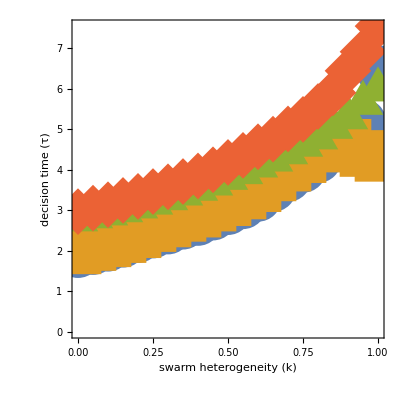

```mathematica
legend=LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;4]],AbsoluteThickness[10]]],{"DS WA", "DS DoS", "CI WA", "CI DoS"},LegendMarkerSize->48,LegendFunction->"Frame",LabelStyle->{FontSize->50}];

ListPlot[{avgTimesDSWA, avgTimesDSDoS, avgTimesCIWA, avgTimesCIDoS},(* PlotLegends->Placed[legend, Above],*)
		Frame->True,
		   ImageSize->Full,
		PlotMarkers->{ {"●",48}, {"■", 48}, {"▲", 48},{"◆", 48} },
		FrameLabel->{Style[Row[{
								 Style["swarm heterogeneity (", Bold, 72, Black],
								  Style["k", Bold, 72, FontSlant -> Italic, Black],
								    Style[")", Bold, 72, Black]
								  }], 56, Bold, Black, SingleLetterItalics->True], Style["decision time (τ)", 56, Bold, Black, SingleLetterItalics->True]},
FrameTicksStyle->Directive[Black,56],
AspectRatio->1
]
```

### Plotting average decision deadlock proportion CHDS, CHCI, WA, DoS

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
path = "/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/";
gName = "G_8/";
zWAName = "za_0";
zDosName = "za_0_0_5";
G=8;
n=1;
pathDSWA = path<>"chds/"<>gName<>"more_a/za_0/";
pathDSDoS = path<>"chds/"<>gName<>"more_a/za_0_0_5/";
pathCIWA = path<>"chci/"<>gName<>"more_a/za_0/";
pathCIDoS = path<>"chci/"<>gName<>"more_a/za_0_0_5/";

proportionDSWA={};
proportionDSDoS = {};
proportionCIWA ={};
proportionCIDoS={};

Do[
za=0.00;
suffix = ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt";
awinspointsDSWA = ToExpression[StringSplit[Import[pathDSWA<>"a_wins_points_k_"<>suffix],"\n"]] ;
awinspointsCIWA = ToExpression[StringSplit[Import[pathCIWA<>"a_wins_points_k_"<>suffix],"\n"]] ;
bwinspointsDSWA = ToExpression[StringSplit[Import[pathDSWA<>"b_wins_points_k_"<>suffix],"\n"]];
bwinspointsCIWA = ToExpression[StringSplit[Import[pathCIWA<>"b_wins_points_k_"<>suffix],"\n"]] ;
deadlockpointsDSWA = ToExpression[StringSplit[Import[pathDSWA<>"deadlock_points_k_"<>suffix],"\n"]] ;
deadlockpointsCIWA = ToExpression[StringSplit[Import[pathCIWA<>"deadlock_points_k_"<>suffix],"\n"]] ;
za=0.05;
suffix = ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt";
awinspointsDSDoS = ToExpression[StringSplit[Import[pathDSDoS<>"a_wins_points_k_"<>suffix],"\n"]] ;
awinspointsCIDoS = ToExpression[StringSplit[Import[pathCIDoS<>"a_wins_points_k_"<>suffix],"\n"]] ;
bwinspointsDSDoS = ToExpression[StringSplit[Import[pathDSDoS<>"b_wins_points_k_"<>suffix],"\n"]] ;
bwinspointsCIDoS = ToExpression[StringSplit[Import[pathCIDoS<>"b_wins_points_k_"<>suffix],"\n"]] ;
deadlockpointsDSDoS = ToExpression[StringSplit[Import[pathDSDoS<>"deadlock_points_k_"<>suffix],"\n"]] ;
deadlockpointsCIDoS = ToExpression[StringSplit[Import[pathCIDoS<>"deadlock_points_k_"<>suffix],"\n"]] ;

AppendTo[proportionDSWA, {k, Length[deadlockpointsDSWA]/(Length[awinspointsDSWA]+Length[bwinspointsDSWA]+Length[deadlockpointsDSWA])}];
AppendTo[proportionDSDoS, {k, Length[deadlockpointsDSDoS]/(Length[awinspointsDSDoS]+Length[bwinspointsDSDoS]+Length[deadlockpointsDSDoS])}];
AppendTo[proportionCIWA, {k, Length[deadlockpointsCIWA]/(Length[awinspointsCIWA]+Length[bwinspointsCIWA]+Length[deadlockpointsCIWA])}];
AppendTo[proportionCIDoS, {k, Length[deadlockpointsCIDoS]/(Length[awinspointsCIDoS]+Length[bwinspointsCIDoS]+Length[deadlockpointsCIDoS])}];
,{k,0,1,0.05}]
```

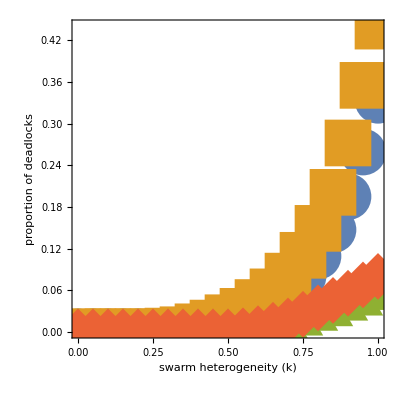

```mathematica
legend=LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;4]],AbsoluteThickness[10]]],{"direct switch - wrong addressing", "direct switch - denial of service", "cross-inhibition - wrong addressing", "cross-inhibition - denial of service"},LegendMarkerSize->48,LegendFunction->"Frame",LabelStyle->{FontSize->30}];

ListPlot[{proportionDSWA, proportionDSDoS, proportionCIWA, proportionCIDoS}, (*PlotLegends->Placed[legend, Above],*)
		Frame->True,
		   ImageSize->Full,
		PlotMarkers->{ {"●",48}, {"■", 48}, {"▲", 48},{"◆", 48} },
PlotRange->Full,
		FrameLabel->{Style[Row[{
								 Style["swarm heterogeneity (", Bold, 72, Black],
								  Style["k", Bold, 72, FontSlant -> Italic, Black],
								    Style[")", Bold, 72, Black]
								  }]], Style["proportion of deadlocks", 56, Bold, Black]},
FrameTicksStyle->Directive[Black,56],
AspectRatio->1
]
```

### Plotting averaged accuracy, regret, convergence time and cognitive cost - direct switch

{{0.,7495/2599},{0.05,7631/2596},{0.1,7874/2593},{0.15,8027/2588},{0.2,8176/2581},{0.25,8477/2575},{0.3,8654/2565},{0.35,8861/2553},{0.4,456/127},{0.45,9448/2525},{0.5,9709/2504},{0.55,10082/2479},{0.6,1051/245},{0.65,3663/805},{0.7,1007/215},{0.75,11322/2305},{0.8,11448/2233},{0.85,833/164},{0.9,10803/2026},{0.95,10227/1885},{1.,11317/1733}}

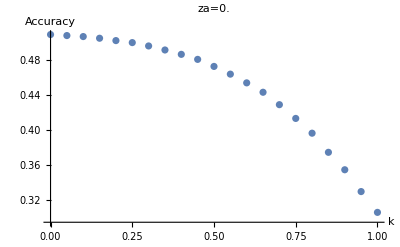

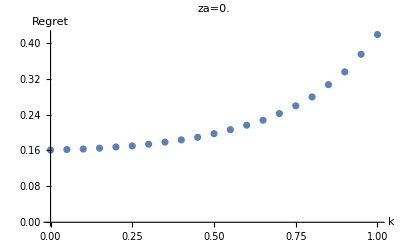

-Graphics-

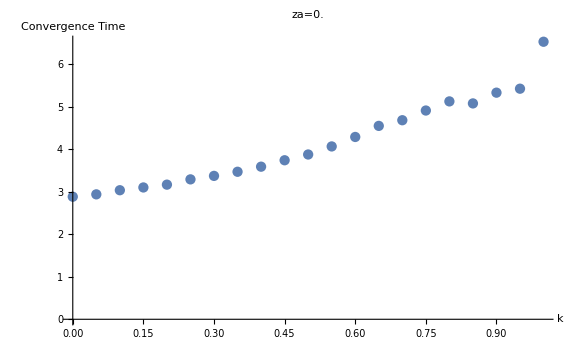

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

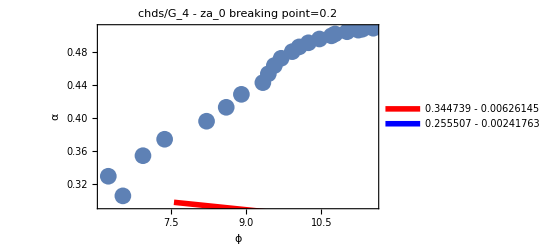

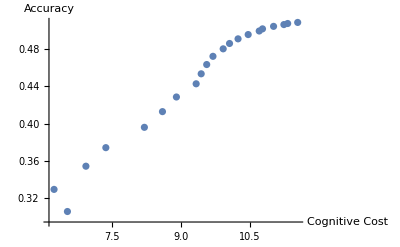

8.4775

{6.23928,856/2601}

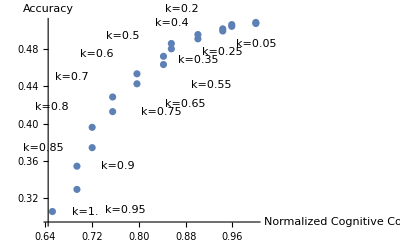

{}

Minimum distance:

6.25369

1.9

{{0.,11.5352},{0.1,11.3172},{0.2,11.2357},{0.3,11.011},{0.4,10.7707},{0.5,10.6996},{0.6,10.4597},{0.7,10.2398},{0.8,10.0547},{0.9,9.91716},{1.,9.69537},{1.1,9.55973},{1.2,9.44048},{1.3,9.33168},{1.4,8.90358},{1.5,8.60147},{1.6,8.20966},{1.7,7.37409},{1.8,6.943},{1.9,6.25369},{2.,6.54588}}

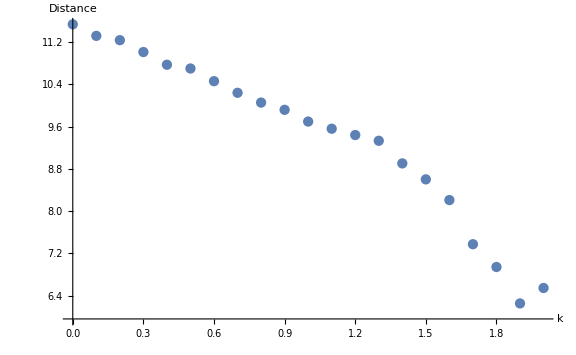

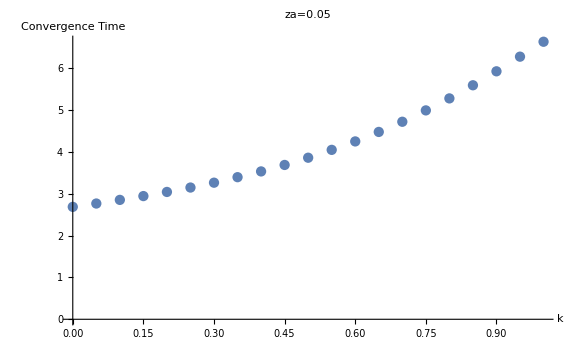

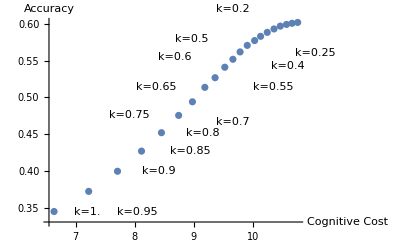

6.63887

{6.63706,898/2601}k=1.

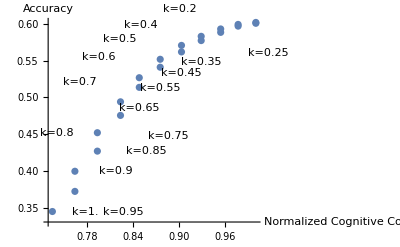

{}

Minimum distance:

6.65635

2.

{{0.,10.7528},{0.1,10.6575},{0.2,10.5638},{0.3,10.4592},{0.4,10.3534},{0.5,10.2392},{0.6,10.1269},{0.7,10.0262},{0.8,9.90223},{0.9,9.78188},{1.,9.66137},{1.1,9.52426},{1.2,9.36141},{1.3,9.1892},{1.4,8.98077},{1.5,8.74914},{1.6,8.46036},{1.7,8.1254},{1.8,7.72212},{1.9,7.23816},{2.,6.65635}}

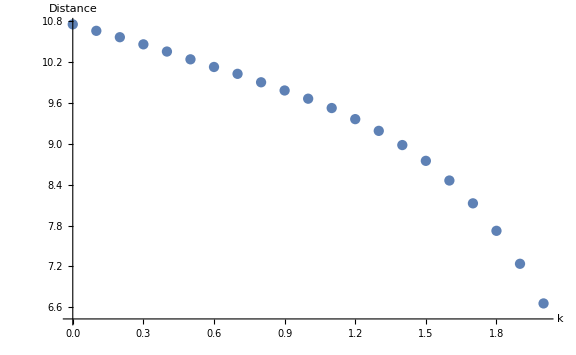

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chds/G_4";
G=4;
zName = "za_0" (*as before*);
path="polimi/Magistrale/secondo_anno/thesis/notebooks/";
za=0.0;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
n=15;
costAccuracyList={};
averagedMetrics =GetAveragedMetrics[za, path1, path3, n, G];
accuracies = averagedMetrics[[1]];
regrets = averagedMetrics[[2]];
convergenceTimes = averagedMetrics[[3]]
costs={};
pointsToDisplay=List[];
kStart=0.3;
kEnd=0.5;
testTimes={};
Graphics[ListPlot[accuracies, AxesLabel->{"k","Accuracy"}, PlotLabel->"za="<>ToString[za]]]
Graphics[ListPlot[regrets, AxesLabel->{"k","Regret"}, PlotLabel->"za="<>ToString[za]]]
accuracyPlot = ListPlot[
accuracies,
PlotStyle->Blue,
ImagePadding->70,
Frame->{True,True,True,False},
FrameLabel->{Style["k",Bold,16],Style["Accuracy", Bold, 16]},
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Blue, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16]},   
PlotLabel->Style["za="<>ToString[za],Bold,16], 
ImageSize->Full
];
regretPlot =  ListPlot[regrets, 
PlotStyle->Red,
ImagePadding->70,
Axes->False, 
Frame->{False,False,False, True}, 
FrameLabel->{{"h",Style["Regret", Bold, 16]},{"h","H"}},
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Red, Thick, FontSize->16]},
FrameTicks->{{None,All},{None,None}}, 
ImageSize->Full,
TicksStyle->Large];
ImageCompose[accuracyPlot, regretPlot]
Graphics[ListPlot[convergenceTimes,  AxesLabel->{Style["k", Bold, 16],Style["Convergence Time", Bold, 16]}, PlotLabel->"za="<>ToString[za], PlotRange->Full, ImageSize->Large]]
speedAccuracyList = {};
Do[
AppendTo[speedAccuracyList,Labeled[ {convergenceTimes[[i]][[2]], accuracies[[i]][[2]]}, Text[Style["k="<>ToString[i*0.1-0.1], Bold, 16]]]]
,{i,1,Length[accuracies]}];
Graphics[ListPlot[speedAccuracyList, AxesLabel->{Style["Convergence Time", Bold, 16],Style["Accuracy", Bold, 16]}, PlotLabel->"za="<>ToString[za], ImageSize->Full]];
	Do[
	cost=(convergenceTimes[[k*20+1]][[2]])*(k+(1-k)*G); 
AppendTo[costs, cost];
AppendTo[costAccuracyList, {cost, accuracies[[Floor[20*k]+1]][[2]]}], {k,0,1,0.05}];
n = Length[costAccuracyList];
minimumK = -1;
minimumError = +Infinity;

Do[
sublist2=Take[costAccuracyList,k*20];
sublist1=Drop[costAccuracyList,k*20];
fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];

error = fit1["EstimatedVariance"]+fit2["EstimatedVariance"];
If[error<minimumError, minimumK=k;minimumError=error]
,{k,0.1,0.95,0.05}]
sublist2=Take[costRegretList,minimumK*20];
sublist1=Drop[costRegretList,minimumK*20];

fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];

(*Scatter plot*)
scatterPlot=ListPlot[costAccuracyList,PlotStyle->PointSize[0.03]];

(*Line plots for the best-fitting lines*)
linePlot1=Plot[fit1//Normal,{x,Min[sublist1[[All,1]]],Max[sublist1[[All,1]]]},PlotStyle->Directive[Red,Thickness[0.01]],PlotRange->All, PlotLabel->ToString[lineFit1]];

linePlot2=Plot[fit2//Normal,{x,Min[sublist2[[All,1]]],Max[sublist2[[All,1]]]},PlotStyle->Directive[Blue,Thickness[0.01]],PlotRange->All, PlotLabel->ToString[lineFit2]];

(*Show the plots together*)
plot = Show[scatterPlot,linePlot1,linePlot2,AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["ϕ", Bold, Black, 64],Style["α", Bold, Black, 64]},FrameTicks->True, FrameTicksStyle->Directive[Black, Bold, 32],PlotLabel->Style[name<>" - "<>zName<>" breaking point="<>ToString[minimumK], Black, Bold, 32],
ImageSize->Full, FrameStyle->Directive[Black, Bold]];
Legended[plot,Placed[LineLegend[{Directive[Red,Thickness[0.05]],Directive[Blue,Thickness[0.05]]},{Style[ToString[fit1//Normal], 32],Style[ToString[fit2//Normal], 32]}], {0.8,0.8}]]


Graphics[ListPlot[costAccuracyList, AxesLabel->{Style["Cognitive Cost", Bold, 16],Style["Accuracy", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]]
MinDistance[costAccuracyList, {0,0.5}]
(*Export["path/folder/costacc_za_0.txt",costAccuracyList];*) (*allows to condense two cost accuracy graphs later, one per za*)
maxAccuracy = N[Max[Take[Flatten[accuracies], {2,Length[accuracies]*2, 2}]]];
maxCost = Max[costs];
remapCosts[x_]:=(x-Min[costs])/(Max[costs]-Min[costs]);
normalizedCosts = Map[remapCosts, costs];
normalizedCostAccuracyList = {};
Do[
AppendTo[normalizedCostAccuracyList, Labeled[{normalizedCosts[[Floor[10*k]+1]], accuracies[[Floor[20*k]+1]][[2]]}, Text["k="<>ToString[k]]]]
,{k,0,1,0.05}];
ListPlot[normalizedCostAccuracyList, AxesLabel->{Style["Normalized Cognitive Cost", Bold, 16],Style["Accuracy", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]
Export[path<>name<>"/costacc_"<>zName<>".txt",costAccuracyList];
alfa = maxAccuracy/maxCost;
minDist=+Infinity;
minK=1;
distances={}
Do[
d = Sqrt[(costs[[i]])^2+(maxAccuracy-accuracies[[i,2]])];
AppendTo[distances, {N[(i-1)/10], d}];
If[d<minDist, minDist = d; minK=N[(i-1)/10]]
,{i,1,Length[costs]}]
Print["Minimum distance:"]
minDist
minK
distances
Export[path<>name<>"/distances_"<>zName<>".txt",distances]; (*allows to condense two distance graphs later, one per za*)
ListPlot[distances, 
AxesLabel->{Style["k", Bold, 16],Style["Distance", Bold, 16]},
ImageSize->Large,
PlotRange->Full]
```

### Plotting the condensed cost/accuracy and distance graphs for za=0,0.05 - direct switch

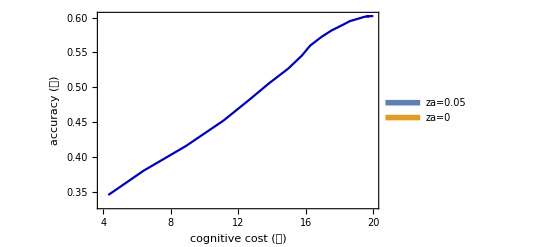

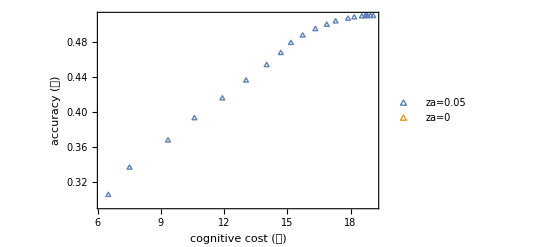

-Graphics-

-Graphics-

```mathematica
name="chds/G_8";
path="polimi/Magistrale/secondo_anno/thesis/notebooks/";
icaZa005 = Import[path<>name<>"/costacc_za_0_0_5.txt"];
caZa005 = ToExpression[StringSplit[icaZa005, "\n"]];
dZa005 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0_0_5.txt"], "\n"]];
icaZa0 = Import[path<>name<>"/costacc_za_0.txt"];
caZa0 = ToExpression[StringSplit[icaZa0, "\n"]];
dZa0 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0.txt"], "\n"]];
legend = LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;2]],AbsoluteThickness[10]]],{"za=0.05","za=0"},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->56}];

p1 = ListPlot[caZa005, 
ColorFunction->Function[{x,y},RGBColor[0,0,x]],Joined->True,
Frame->True,
FrameLabel->{Style["cognitive cost (𝜙)", Bold, 56],Style["accuracy (𝛼)", Bold, 56]},
FrameTicksStyle->Directive[Black,48],
 ImageSize->Full,PlotRange->Full, 
LabelStyle->Directive[Black, Large] ,  
PlotLegends->Placed[legend, Top], 
AxesStyle->Directive[Black, 32]]
p2 =  ListPlot[{caZa0}, 
ColorFunction->"BlueGreenYellow",
Frame->True,
FrameLabel->{Style["cognitive cost (𝜙)", Bold, 56],Style["accuracy (𝛼)", Bold, 56]},
PlotMarkers->△,
FrameTicksStyle->Directive[Black,48],
 ImageSize->Full,PlotRange->Full, 
LabelStyle->Directive[Black, Large] ,  
PlotLegends->Placed[legend, Top], 
AxesStyle->Directive[Black, 32]]
p = Rasterize[ListPlot[{caZa005, caZa0}, 
PlotMarkers->{{●,0.5},{ ▲,0.5}},
Frame->True,
FrameLabel->{Style["cognitive cost (𝜙)", Bold, 56],Style["accuracy (𝛼)", Bold, 56]},
FrameTicksStyle->Directive[Black,48],
 ImageSize->Full,PlotRange->Full, 
LabelStyle->Directive[Black, Large] ,  
PlotLegends->Placed[legend, Top], 
AxesStyle->Directive[Black, 32]]]
p1 = Rasterize[ListPlot[{dZa005, dZa0}, 
AxesLabel->{Style["k", Bold, 32],Style["Distance", Bold, 32]},
ImageSize->Full,
PlotRange->Full,
 PlotLegends->Placed[legend, Top]
, AxesStyle->Directive[Black, 32]]];
```

### Same as before but for cross-inhibition

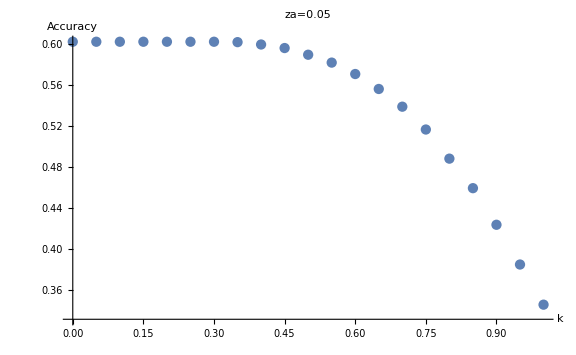

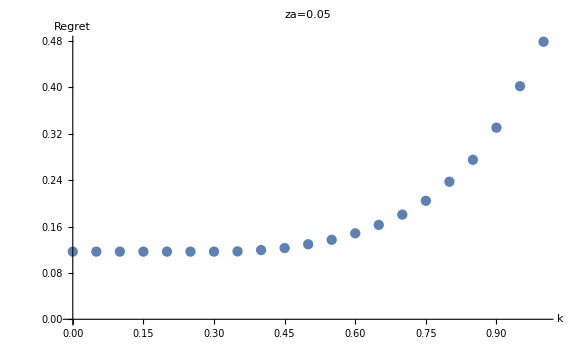

-Graphics-

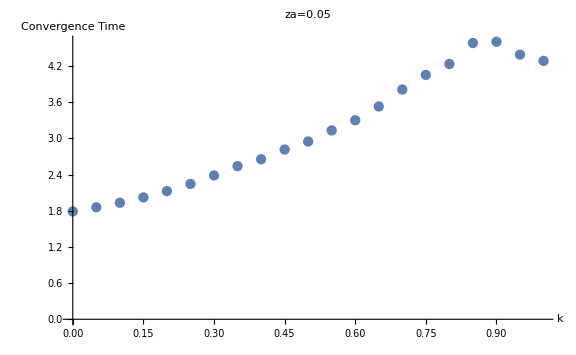

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

-0.0297623

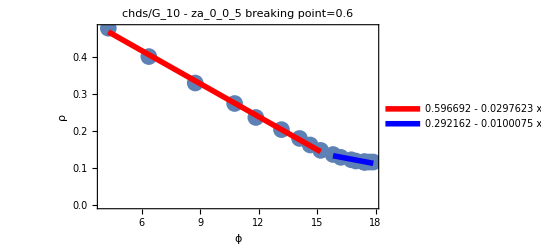

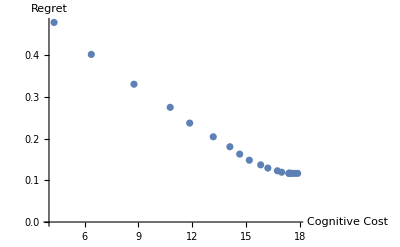

6.06216

2.

{{0.,25.2938},{0.1,25.0902},{0.2,24.8778},{0.3,24.7293},{0.4,24.6555},{0.5,24.6045},{0.6,24.6325},{0.7,24.6134},{0.8,24.0301},{0.9,23.691},{1.,22.9377},{1.1,22.3727},{1.2,21.4763},{1.3,20.7153},{1.4,19.942},{1.5,18.6288},{1.6,16.7691},{1.7,15.2298},{1.8,12.3708},{1.9,9.00259},{2.,6.06216}}

polimi/Magistrale/secondo_anno/thesis/notebooks/chds/G_10/distances_za_0_0_5.txt

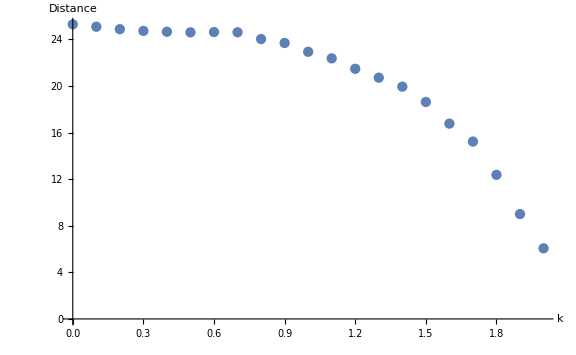

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chds/G_10";
G=10;
zName="za_0_0_5";
za=0.05;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
n=15;
costRegretList={};
averagedMetrics =GetAveragedMetrics[za, path1, path3, n, G];
accuracies = averagedMetrics[[1]];
regrets = averagedMetrics[[2]];
convergenceTimes = averagedMetrics[[3]];
costs={};
Graphics[ListPlot[accuracies, AxesLabel->{"k","Accuracy"}, PlotLabel->"za="<>ToString[za]]]
Graphics[ListPlot[regrets, AxesLabel->{"k","Regret"}, PlotLabel->"za="<>ToString[za]]]
accuracyPlot = ListPlot[
accuracies,
PlotStyle->Blue,
ImagePadding->100,
Frame->{True,True,True,False},
FrameLabel->{Style["k",Bold,30],Style["Accuracy", Bold, 16]},
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Blue, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16]},   
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameTicksStyle->Directive[25],
ImageSize->Full
];
regretPlot =  ListPlot[regrets, 
PlotStyle->Red,
ImagePadding->100,
Axes->False, 
Frame->{False,False,False, True}, 
FrameLabel->{{"h",Style["Regret", Bold, 16]},{"h","H"}},
PlotLabel->Style["za="<>ToString[za],Bold,16], 
FrameStyle->{Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Black, Thick, FontSize->16],Directive[Red, Thick, FontSize->16]},
FrameTicks->{{None,All},{None,None}}, 
ImageSize->Full,
TicksStyle->Large,
FrameTicksStyle->Directive[25]];
ImageCompose[accuracyPlot, regretPlot]
Graphics[ListPlot[convergenceTimes,  AxesLabel->{Style["k", Bold, 16],Style["Convergence Time", Bold, 16]}, PlotLabel->"za="<>ToString[za], PlotRange->Full, ImageSize->Large]]
(*plot the normalized regret*)
Do[
	cost=(convergenceTimes[[k*20+1]][[2]](*+stds[[k*10+1]][[2]][[2]]*))*(k+(1-k)*G); 
AppendTo[costs, cost];
, {k,0,1,0.05}];
Do[
(*AppendTo[costRegretList, Labeled[{costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]]}, Text["k="<>ToString[k]]]]*)
AppendTo[costRegretList,{costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]]}]
,{k,0,1,0.05}];

minimumK = -1;
minimumError = +Infinity;

Do[
sublist2=Take[costRegretList,k*20];
sublist1=Drop[costRegretList,k*20];
fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];

error = fit1["EstimatedVariance"]+fit2["EstimatedVariance"];
If[error<minimumError, minimumK=k;minimumError=error]
,{k,0.1,0.95,0.05}]
sublist2=Take[costRegretList,minimumK*20];
sublist1=Drop[costRegretList,minimumK*20];

fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];


(*Scatter plot*)
scatterPlot=ListPlot[costRegretList,PlotStyle->PointSize[0.03]];

(*Line plots for the best-fitting lines*)
linePlot1=Plot[fit1//Normal,{x,Min[sublist1[[All,1]]],Max[sublist1[[All,1]]]},PlotStyle->Directive[Red,Thickness[0.01]],PlotRange->All, PlotLabel->ToString[lineFit1]];

linePlot2=Plot[fit2//Normal,{x,Min[sublist2[[All,1]]],Max[sublist2[[All,1]]]},PlotStyle->Directive[Blue,Thickness[0.01]],PlotRange->All, PlotLabel->ToString[lineFit2]];

(*Show the plots together*)
plot = Show[scatterPlot,linePlot1,linePlot2,AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["ϕ", Bold, Black, 64],Style["ρ", Bold, Black, 64]},FrameTicks->True, FrameTicksStyle->Directive[Black, Bold, 32],PlotLabel->Style[name<>" - "<>zName<>" breaking point="<>ToString[minimumK], Black, Bold, 32],
ImageSize->Full, FrameStyle->Directive[Black, Bold]];
Legended[plot,Placed[LineLegend[{Directive[Red,Thickness[0.05]],Directive[Blue,Thickness[0.05]]},{Style[ToString[fit1//Normal], 32],Style[ToString[fit2//Normal], 32]}], {0.8,0.8}]]


Export["polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/costreg_"<>zName<>".txt",costRegretList];
Graphics[ListPlot[costRegretList, AxesLabel->{Style["Cognitive Cost", Bold, 16],Style["Regret", Bold, 16]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large]]]
distances={};
minDist=+Infinity;
minK=0.0;
Do[
d = EuclideanDistance[{0,0}, costRegretList[[i]][[1]]];
AppendTo[distances, {N[(i-1)/10], d}];
If[d<minDist, minDist = d; minK=N[(i-1)/10]]
,{i,1,Length[costs]}]
minDist
minK
distances
Export["polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/distances_"<>zName<>".txt",distances]
ListPlot[distances, 
AxesLabel->{Style["k", Bold, 16],Style["Distance", Bold, 16]},
ImageSize->Large,
PlotRange->Full]
```

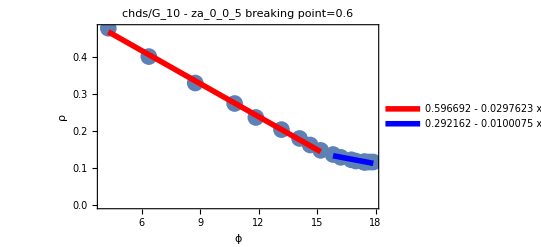

-Graphics-

6.06216

2.

{{0.,25.2938},{0.1,25.0902},{0.2,24.8778},{0.3,24.7293},{0.4,24.6555},{0.5,24.6045},{0.6,24.6325},{0.7,24.6134},{0.8,24.0301},{0.9,23.691},{1.,22.9377},{1.1,22.3727},{1.2,21.4763},{1.3,20.7153},{1.4,19.942},{1.5,18.6288},{1.6,16.7691},{1.7,15.2298},{1.8,12.3708},{1.9,9.00259},{2.,6.06216}}

polimi/Magistrale/secondo_anno/thesis/notebooks/chds/G_10/distances_za_0_0_5.txt

-Graphics-

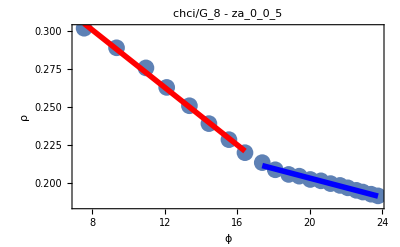

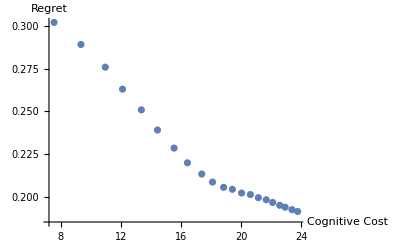

10.6796

2.

{{0.,33.6018},{0.1,33.0635},{0.2,32.42},{0.3,31.9124},{0.4,31.2455},{0.5,30.6386},{0.6,29.9012},{0.7,29.1504},{0.8,28.3215},{0.9,27.4595},{1.,26.6352},{1.1,25.589},{1.2,24.5743},{1.3,23.2266},{1.4,21.9751},{1.5,20.4135},{1.6,18.8927},{1.7,17.1204},{1.8,15.5018},{1.9,13.2092},{2.,10.6796}}

polimi/Magistrale/secondo_anno/thesis/notebooks/chci/G_8/distances_za_0_0_5.txt

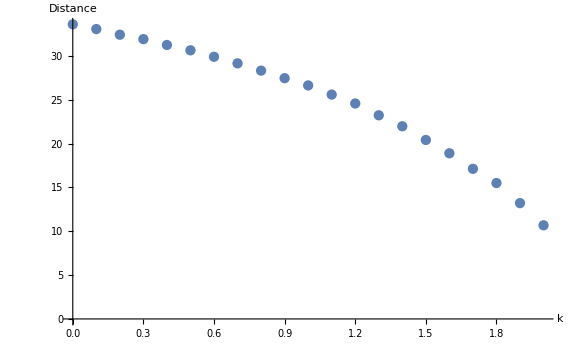

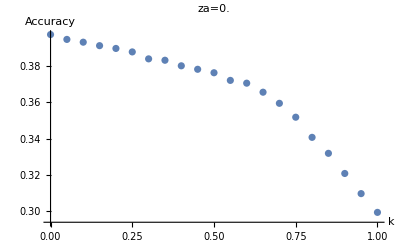

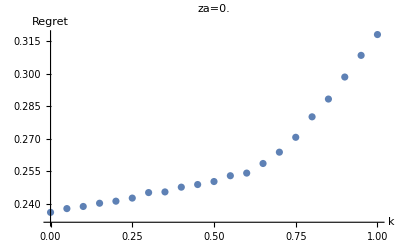

-Graphics-

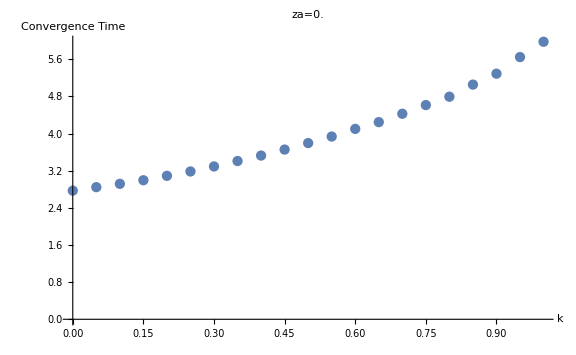

{{22.1699,0.236178},{21.7765,0.237916},{21.3022,0.238893},{20.8206,0.240384},{20.3963,0.24133},{19.9034,0.242753},{19.4285,0.24529},{18.9225,0.24559},{18.3409,0.247782},{17.733,0.248989},{17.083,0.250373},{16.3383,0.253041},{15.5858,0.254256},{14.6555,0.25867},{13.7257,0.263883},{12.6911,0.270727},{11.5083,0.280146},{10.3648,0.288328},{8.99547,0.298462},{7.6262,0.308428},{5.97939,0.318008}}

-0.00683931

0.25867

0.358903

-0.00274566

0.254256

0.297049

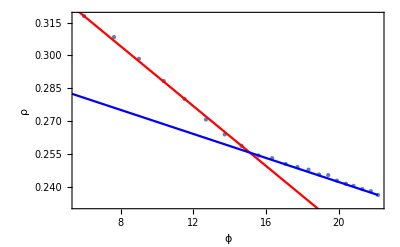

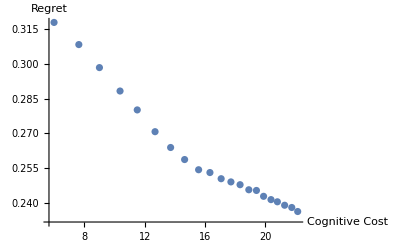

8.45614

2.

{{0.,31.353},{0.1,30.7966},{0.2,30.1258},{0.3,29.4448},{0.4,28.8447},{0.5,28.1477},{0.6,27.476},{0.7,26.7604},{0.8,25.938},{0.9,25.0782},{1.,24.1591},{1.1,23.1059},{1.2,22.0417},{1.3,20.726},{1.4,19.411},{1.5,17.9479},{1.6,16.2753},{1.7,14.658},{1.8,12.7215},{1.9,10.7851},{2.,8.45614}}

polimi/Magistrale/secondo_anno/thesis/notebooks/chci/G_8/distances_za_0.txt

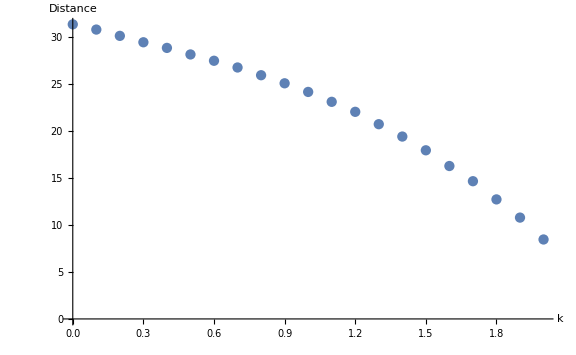

```mathematica
Directive
```

```mathematica
path="polimi/Magistrale/secondo_anno/thesis/notebooks/";
icaZa005 = Import[path<>name<>"/costreg_za_0_0_5.txt"];
caZa005 = ToExpression[StringSplit[icaZa005, "\n"]];
dZa005 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0_0_5.txt"], "\n"]];
icaZa0 = Import[path<>name<>"/costreg_za_0.txt"];
caZa0 = ToExpression[StringSplit[icaZa0, "\n"]];
dZa0 =  ToExpression[StringSplit[ Import[path<>name<>"/distances_za_0.txt"], "\n"]];
legend = LineLegend[Thread[Directive[ColorData[97,"ColorList"][[;;2]],AbsoluteThickness[10]]],{"za=0.05","za=0"},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
p = Rasterize[ListPlot[{caZa005, caZa0}, AxesLabel->{Style["Cognitive Cost", Bold, 32],Style["Regret", Bold, 32]}, ImageSize->Full,PlotRange->Full, LabelStyle->Directive[Black, Large] ,  PlotLegends->Placed[legend, Top], AxesStyle->Directive[Black, 32]]]
p1 = Rasterize[ListPlot[{dZa005, dZa0}, 
AxesLabel->{Style["k", Bold, 32],Style["Distance", Bold, 32]},
ImageSize->Full,
PlotRange->Full,
 PlotLegends->Placed[legend, Top]
, AxesStyle->Directive[Black, 32]]]
```

-Graphics-

-Graphics-

```mathematica
(*m1 = ExtractK[za, path1];
m2 = ExtractK[za, path2];
m3 = ExtractK[za, path3];*)
(*accuracies = {};
regrets = {};
convergenceTimes = {};
testTimes={};
stds={};
costs={};
pointsToDisplay=List[];
kStart=0.3;
kEnd=0.5
Do[
a1 = m1[[1]][[k*10+1]][[2]];
a2 = m2[[1]][[k*10+1]][[2]];
a3 = m3[[1]][[k*10+1]][[2]];
a = (a1+a2+a3)/3;
r = (m1[[2]][[k*10+1]][[2]]+m2[[2]][[k*10+1]][[2]]+m3[[3]][[k*10+1]][[2]])/3;
timeList1 = m1[[5]][[k*10+1]];
timeList2 = m2[[5]][[k*10+1]];
timeList3 = m3[[5]][[k*10+1]];
timeList = Join[timeList1, timeList2, timeList3];
onlyTimeList = timeList[[All,3]];
AppendTo[accuracies, {k, a}];
AppendTo[regrets, {k,r}];
AppendTo[convergenceTimes, {k, Total[onlyTimeList]/Length[onlyTimeList]}];
AppendTo[stds, {k, PlusMinus[(m1[[3,k*10+1, 2]]+m2[[3,k*10+1,2]]+m3[[3,k*10+1,2]])/3,(m1[[4,k*10+1, 2,2]]+m2[[4,k*10+1,2,2]]+m3[[4,k*10+1,2,2]])/3 ]}];
,{k,0,1,0.1}]*)
```

-Graphics-

### Plotting the parameter space of a heterogeneous model, showing the change for 3 values of k

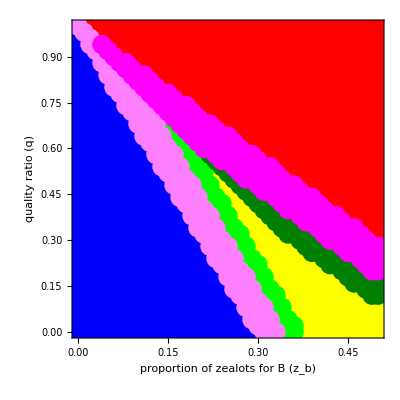

```mathematica
path =  "/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/chds/G_8/more_a/za_0/";
za=0.0;
awinspoints={};
bwinspoints={};
deadlockpoints={};
pointsToDisplay=List[];
Do[
awinspoints = ToExpression[StringSplit[Import[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]] ;
bwinspoints =ToExpression[StringSplit[ Import[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
deadlockpoints =ToExpression[StringSplit[Import[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
AppendTo[pointsToDisplay, {awinspoints, bwinspoints, deadlockpoints, k}];
, {k,0.8,1,0.1}];
awinsPointsK08 = pointsToDisplay[[1,1]];
bwinsPointsK08 = pointsToDisplay[[1,2]];
deadlockPointsK08=pointsToDisplay[[1,3]];
awinsPointsK09 = pointsToDisplay[[2,1]];
bwinsPointsK09 = pointsToDisplay[[2,2]];
deadlockPointsK09=pointsToDisplay[[2,3]];
awinsPointsK1 = pointsToDisplay[[3,1]];
bwinsPointsK1 = pointsToDisplay[[3,2]];
deadlockPointsK1=pointsToDisplay[[3,3]];
commonAPoints={};
commonBPoints={};
commonDeadlockPoints={};
firstDeadlockPointsBottom={}; (*points that are associated to the victory of A in k=0.9 but resulted in a deadlock in k=1*)
secondDeadlockPointsBottom={};(*points that are associated to the victory of A in k=0.8 but resulted in a deadlock in k=0.9*)
firstDeadlockPointsTop={};(*points that are associated to the victory of B in k=0.9 but resulted in a deadlock in k=1*)
secondDeadlockPointsTop={};(*points that are associated to the victory of B in k=0.8 but resulted in a deadlock in k=0.9*)
Do[
If[MemberQ[ awinsPointsK08,{zb,q}]&&MemberQ[awinsPointsK1,{zb,q}], AppendTo[commonAPoints, {zb,q}],
If[MemberQ[ bwinsPointsK08,{zb,q}]&&MemberQ[bwinsPointsK09,{zb,q}]&&MemberQ[ bwinsPointsK1,{zb,q}], AppendTo[commonBPoints, {zb,q}], 
If[MemberQ[ deadlockPointsK08,{zb,q}]&&MemberQ[deadlockPointsK09,{zb,q}]&&MemberQ[ deadlockPointsK1,{zb,q}], AppendTo[commonDeadlockPoints, {zb,q}],
If[MemberQ[ awinsPointsK08,{zb,q}]&&MemberQ[deadlockPointsK09,{zb,q}], AppendTo[secondDeadlockPointsBottom, {zb,q}],
If[MemberQ[ awinsPointsK09,{zb,q}]&&MemberQ[ deadlockPointsK1,{zb,q}], AppendTo[firstDeadlockPointsBottom, {zb,q}],
If[MemberQ[ bwinsPointsK08,{zb,q}]&&MemberQ[ deadlockPointsK09,{zb,q}], AppendTo[secondDeadlockPointsTop, {zb,q}],
AppendTo[firstDeadlockPointsTop, {zb,q}]
]

]
]]]]
, {zb,0,0.5,0.01}, {q,0(*0 for p_alfa, 0.01 for combinatorial*),1,0.02}]
ListPlot[{commonAPoints, commonBPoints, commonDeadlockPoints, secondDeadlockPointsBottom, firstDeadlockPointsBottom, secondDeadlockPointsTop, firstDeadlockPointsTop}, PlotStyle->{Blue, Red, Yellow,Green, RGBColor[1,0.5,1],RGBColor[0,0.5,0], RGBColor[1,0,1]}, 
ImageSize->Full, 
LabelStyle->Directive[Black],
PlotRangePadding -> {Automatic, 0.02},
FrameLabel->{Style["proportion of zealots for B (z_b)", Bold, 72, SingleLetterItalics->True],Row[{
								 Style["quality ratio (", Bold, 72, Black],
								  Style["q", Bold, 72, FontSlant -> Italic, Black],
								    Style[")", Bold, 72, Black]
								  }]}, 
							ImageSize->Full, LabelStyle->Directive[Black, Large], 
							PlotMarkers->{"●", 20},
							AspectRatio->1,
							Frame->True,
							FrameTicks->True,
							FrameTicksStyle->Directive[Black,48]]
```

```mathematica
ListPlot[{commonAPoints, commonBPoints, commonDeadlockPoints, secondDeadlockPointsBottom, firstDeadlockPointsBottom, secondDeadlockPointsTop, firstDeadlockPointsTop}, PlotStyle->{Blue, Red, Yellow,Green, RGBColor[1,0.5,1],RGBColor[0,0.5,0], RGBColor[1,0,1]}, AxesLabel->{Style["zb", Bold, 32],Style["q", Bold, 32]}, ImageSize->Full, LabelStyle->Directive[Black, Large]]
```

ListPlot::lpn: {{},{},{},{},{},{},{{0.001,0.},{0.001,0.01},{0.001,0.02},{0.001,0.03},{0.001,0.04},{0.001,0.05},{0.001,0.06},{0.001,0.07},{0.001,0.08},{0.001,0.09},«10090»}} is not a list of numbers or pairs of numbers.

### plotting the parameter space of a model

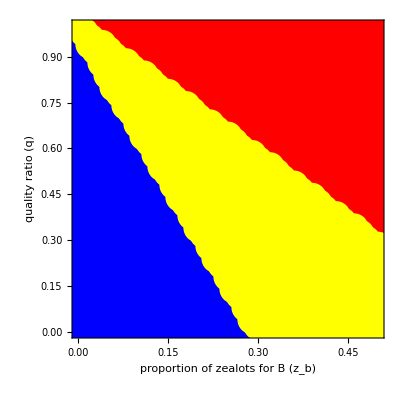

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
plt1 = ParameterSpaceK[1, 0.0, "/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/chds/G_8/more_a/za_0/"]
```

1566

1035

0

2601

0.116724

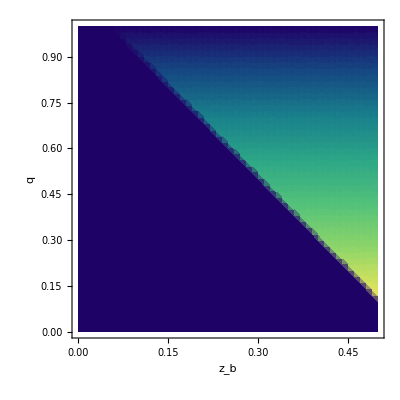

-Graphics-

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
path ="personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>"chds/G_8/"<>"more_a/za_0_0_5/";
k=0.1;
za=0.05;
awinspoints = ToExpression[StringSplit[Import[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]] ;
bwinspoints =ToExpression[StringSplit[ Import[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
deadlockpoints =ToExpression[StringSplit[Import[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
regretValueList = {};
Do[
AppendTo[regretValueList,{awinspoints[[i]][[1]], awinspoints[[i]][[2]], 0}];
,{i, 1, Length[awinspoints]}];
Do[
AppendTo[regretValueList,{bwinspoints[[i]][[1]], bwinspoints[[i]][[2]], 1- bwinspoints[[i]][[2]]}];
,{i, 1, Length[bwinspoints]}];
Do[
AppendTo[regretValueList,{deadlockpoints[[i]][[1]], deadlockpoints[[i]][[2]], 1}];
,{i, 1, Length[deadlockpoints]}];
Length[awinspoints]
Length[bwinspoints]
Length[deadlockpoints]
npoints=Length[awinspoints]+Length[bwinspoints]+Length[deadlockpoints]
regretValueList
sumThirdPosition=Total[regretValueList[[All,3]]]/npoints
plt2 = ListDensityPlot[regretValueList, ColorFunction->"BlueGreenYellow",Frame->True, FrameStyle->Directive[Black, 72], FrameLabel->{Style["z_b",Bold, 96, Black, Italic],Style["q",Bold, 96, Black, Italic]
							(*Row[{
								 Style["quality ratio (", Bold, 72, Black],
								  Style["q", Bold, 72, FontSlant -> Italic, Black],
								    Style[")", Bold, 72, Black]
								  }]*)},FrameTicks->{True,True},
							FrameTicksStyle->Directive[Black,72], ImageSize->Full, PlotRange->All,PlotRangeClipping->False,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"regret (ρ)", LegendMarkerSize->{1300, 100}, LabelStyle->Directive[Black, 120]], Above],
ColorFunctionScaling->True,ClippingStyle->Automatic, ImageSize->Large, PlotRangePadding -> {0.005, 0.01}]



Rasterize[ListDensityPlot[regretValueList, ColorFunction->"BlueGreenYellow",Frame->True, FrameStyle->Directive[Bold, 72], FrameLabel->{Style["proportion of zealots B (z_b)",Black, 72],Style["quality ratio (q)",Black, 72, SingleLetterItalics->True]},FrameTicks->True,
							FrameTicksStyle->Directive[Black,72], ImageSize->300,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"regret (ρ)", LegendMarkerSize->{1400, 100}, LabelStyle->Directive[Bold, 120]], Above], PlotRange->All,PlotRangeClipping->False,PlotRangePadding->0,ColorFunctionScaling->True,ClippingStyle->Automatic]]
```

```mathematica
Total[regretValueList[[3]]]/(npoints)
regrets
```

2601

0.0000153787

{{0.,0.116724},{0.05,0.116724},{0.1,0.116724},{0.15,0.116724},{0.2,0.116724},{0.25,0.116724},{0.3,0.117878},{0.35,0.1198},{0.4,0.124029},{0.45,0.129412},{0.5,0.137101},{0.55,0.146328},{0.6,0.159016},{0.65,0.173403},{0.7,0.192987},{0.75,0.216501},{0.8,0.245621},{0.85,0.285152},{0.9,0.3408},{0.95,0.407928},{1.,0.478731}}

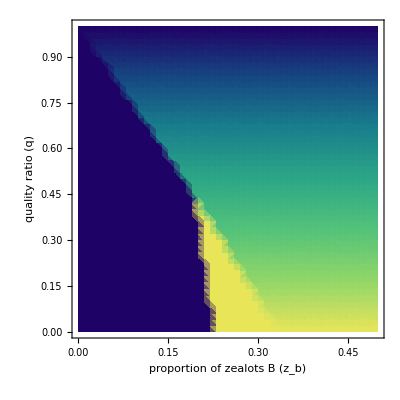

```mathematica
GraphicsRow[{plt1, plt2}]
```

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
names={"chds/G_8/", "chci/G_8/"};
zNames = {"za_0/", "za_0_0_5/"};
zas = {0, 0.05};
matrixList=List[];
Do[
Print["hello"];
plotMatrix=List[];
Do[
plotRow = List[];
Do[

name = names[[nameIndex]];
zName = zNames[[zIndex]];
za = zas[[zIndex]];
path ="personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"more_a/"<>zName;
plot = PlotRegret[path, k, za ];
AppendTo[plotRow, plot];
,{k, 0, 1, 0.05}];
AppendTo[plotMatrix, plotRow];
, {zIndex, 1, Length[zNames]}];
AppendTo[matrixList, plotMatrix];
,  {nameIndex, 1, Length[names]}]
```

hello

hello

```mathematica
ncols = Length[matrixList[[1]][[1]]]
```

21

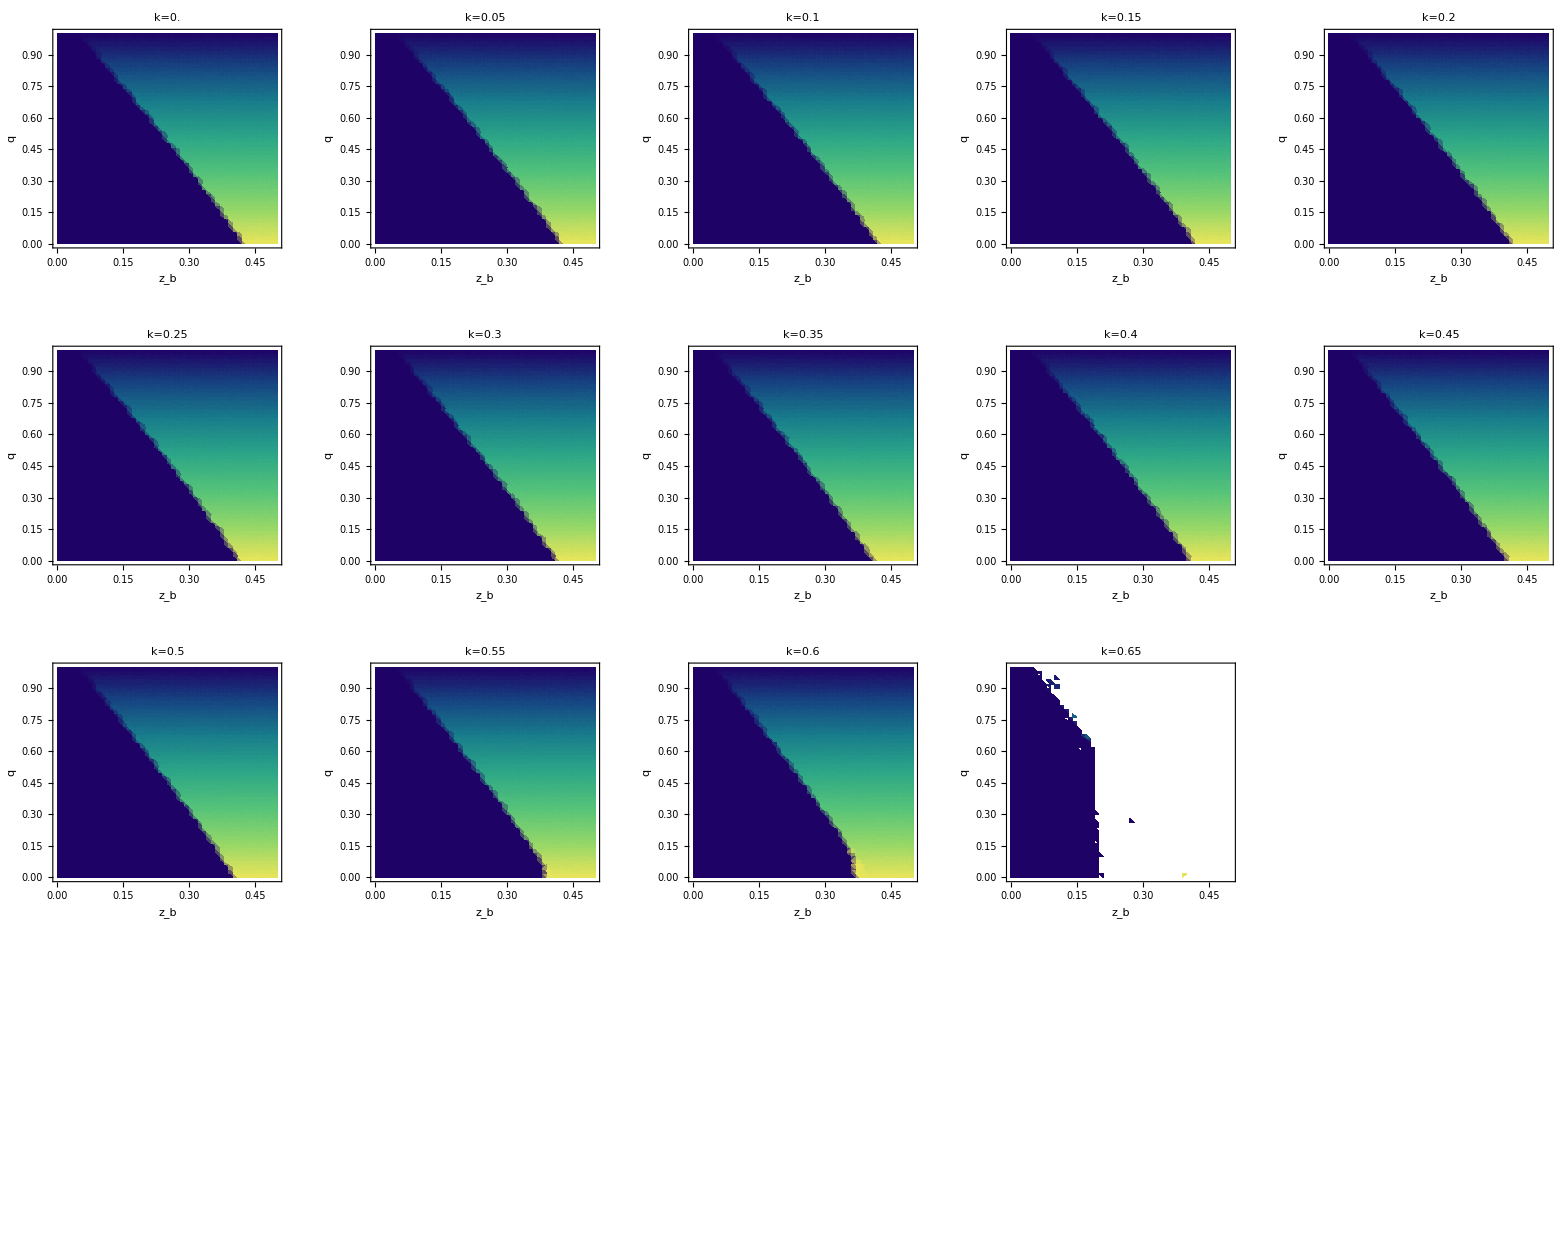

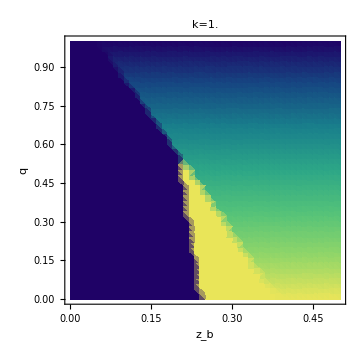

```mathematica
model=2;
attack=2;
GraphicsGrid[{matrixList[[model]][[attack]][[1;;5]],matrixList[[model]][[attack]][[6;;10]], matrixList[[model]][[attack]][[11;;15]], matrixList[[model]][[attack]][[16;;20]]}, ImageSize->Full]
matrixList[[model]][[attack]][[21]]
```

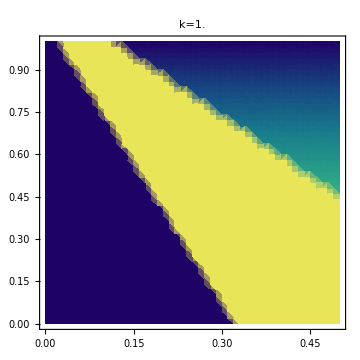

```mathematica
matrixList[[1]][[2]][[21]]
```

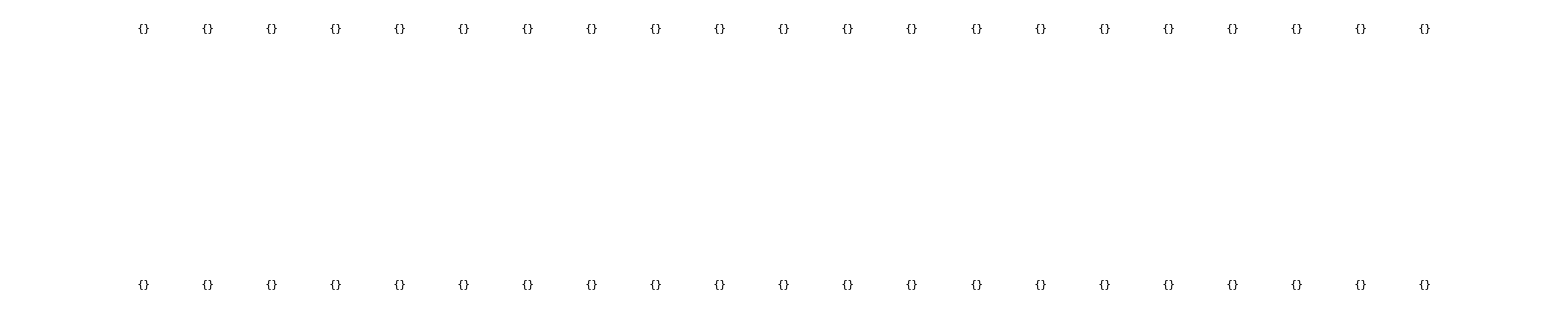

```mathematica
GraphicsGrid[matrixList[[2]], ImageSize->10000]
```

### Bayesian Risk

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl";
name = "chci/G_4";
zName = "za_0";
za=0.0;
n=15;
G=4;
path1 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
metrics = GetAveragedMetrics[za, path1, path3,n, G ];
accuracies = metrics[[1]];
regrets = metrics[[2]];
convergenceTimes = metrics[[3]];
costs = metrics[[4]];
bayesianRiskList = List[];
minimumBRList = List[];
minimumBRValuesList = List[];
Do[
minBR ={{-1,-1}, +Infinity};
Do[
br = costs[[k*20+1]]+h *(regrets[[k*20+1]][[2]]);
AppendTo[bayesianRiskList, {k, h, br}];
If[br<minBR[[2]], minBR = {{k,h}, br}]
,{k,0,1,0.05}];
AppendTo[minimumBRList, minBR[[1]]];
AppendTo[minimumBRValuesList, minBR[[2]]];
,{h,0,300, 0.1}];
(*ListDensityPlot[bayesianRiskList, ColorFunction->"BlueGreenYellow",Axes->True,DataRange->{{0,1},{0,5000}},PlotLabel->Style["Bayesian Risk - "<>name<>" - za="<>ToString[N[za]], 32], FrameLabel->{Style["k", 32], Style["h", 32]}, ImageSize->Full, PlotLegends->Automatic,PlotRange->All,PlotRangeClipping->False,PlotRangePadding->0,ColorFunctionScaling->True,ClippingStyle->Automatic, Epilog->ListPlot[minimumBRList, PlotStyle->{Red,PointSize->0.01}, PlotRange->All][[1]]]*)
```

```mathematica
pl1 = Rasterize[ListDensityPlot[bayesianRiskList, ColorFunction->"BlueGreenYellow",Axes->True,DataRange->{{0,1},{0,100}}, FrameStyle->Directive[Bold, 20],PlotLabel->Style["Bayesian Risk - "<>name<>" - za="<>ToString[N[za]], 32], FrameLabel->{Style["k", 32], Style["h", 32]}, ImageSize->Full, PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->1400, LabelStyle->Directive[Bold, Medium]], Above], PlotRange->All,PlotRangeClipping->False,PlotRangePadding->0,ColorFunctionScaling->True,ClippingStyle->Automatic, Epilog->ListPlot[minimumBRList, PlotStyle->{Red,PointSize->0.01}, PlotRange->All][[1]]]]
```

-Graphics-

```mathematica
30
```

-Graphics-

```mathematica
bayesianRiskList[[101]][[3]]
```

66.9434

```mathematica
Do[
Do[
If[bayesianRiskList[[101*a+b]][[3]]<minimumBRValuesList[[a]], Print[minimumBRList[[a]]]]
,{b,1,100}]
,{a, 0, 100}]
```

```mathematica
Last[bayesianRiskList]
```

{1.,5000,1177.34}

```mathematica
minBR = {0,0,+Infinity};
Do[
If[bayesianRiskList[[i]][[3]]<minBR[[3]], minBR=bayesianRiskList[[i]]]
,{i,1, Length[bayesianRiskList]}]
minBR
maxWeightsList = List[]; (*1 per k*)
minimumBRPerKList = List[];
Do[
maxWeight = -1;
minimumBRPerK = +Infinity;
Do[
target = bayesianRiskList[[(i+1)*(j+1)]];
Print[ToString[N[target]]];
If[target[[3]]==minBR[[3]] && target[[2]]>maxWeight, maxWeight=target[[2]]];
If[target[[3]]<minimumBRPerK, minimmBRPerK = target[[3]]];
,{j, 0, 1000, 100}];
AppendTo[maxWeightsList, maxWeight];
AppendTo[minimumBRPerKList, minimumBRPerK]
,{i, 0, 10(*11 k values*)}]
maxWeightsList
minimumBRPerKList
```

{1.,0,67.5289}

{0., 0., 159.977}

{0., 91., 206.096}

{0., 182., 252.215}

{0., 273., 298.333}

{0., 364., 344.452}

{0., 455., 390.571}

{0., 546., 436.689}

{0., 637., 482.808}

{0., 728., 528.927}

{0., 819., 575.045}

{0.1, 0., 157.171}

{0.1, 91., 203.415}

{0.1, 182., 249.66}

{0.1, 273., 295.905}

{0.1, 364., 342.15}

{0.1, 455., 388.395}

{0.1, 546., 434.639}

{0.1, 637., 480.884}

{0.1, 728., 527.129}

{0.1, 819., 573.374}

{0.2, 0., 152.507}

{0.2, 91., 199.035}

{0.2, 182., 245.562}

{0.2, 273., 292.089}

{0.2, 364., 338.616}

{0.2, 455., 385.143}

{0.2, 546., 431.67}

{0.2, 637., 478.197}

{0.2, 728., 524.725}

{0.2, 819., 571.252}

{0.3, 0., 147.193}

{0.3, 91., 194.192}

{0.3, 182., 241.191}

{0.3, 273., 288.189}

{0.3, 364., 335.188}

{0.3, 455., 382.187}

{0.3, 546., 429.185}

{0.3, 637., 476.184}

{0.3, 728., 523.183}

{0.3, 819., 570.181}

{0.4, 0., 139.921}

{0.4, 91., 187.683}

{0.4, 182., 235.444}

{0.4, 273., 283.206}

{0.4, 364., 330.967}

{0.4, 455., 378.729}

{0.4, 546., 426.49}

{0.4, 637., 474.252}

{0.4, 728., 522.013}

{0.4, 819., 569.775}

{0.5, 0., 131.127}

{0.5, 91., 180.015}

{0.5, 182., 228.902}

{0.5, 273., 277.79}

{0.5, 364., 326.678}

{0.5, 455., 375.566}

{0.5, 546., 424.453}

{0.5, 637., 473.341}

{0.5, 728., 522.229}

{0.5, 819., 571.116}

{0.6, 0., 120.693}

{0.6, 91., 171.179}

{0.6, 182., 221.664}

{0.6, 273., 272.15}

{0.6, 364., 322.635}

{0.6, 455., 373.121}

{0.6, 546., 423.606}

{0.6, 637., 474.092}

{0.6, 728., 524.577}

{0.6, 819., 575.063}

{0.7, 0., 107.153}

{0.7, 91., 159.924}

{0.7, 182., 212.695}

{0.7, 273., 265.466}

{0.7, 364., 318.237}

{0.7, 455., 371.008}

{0.7, 546., 423.779}

{0.7, 637., 476.55}

{0.7, 728., 529.321}

{0.7, 819., 582.092}

{0.8, 0., 93.8399}

{0.8, 91., 149.503}

{0.8, 182., 205.166}

{0.8, 273., 260.829}

{0.8, 364., 316.493}

{0.8, 455., 372.156}

{0.8, 546., 427.819}

{0.8, 637., 483.482}

{0.8, 728., 539.145}

{0.8, 819., 594.808}

{0.9, 0., 77.8426}

{0.9, 91., 137.221}

{0.9, 182., 196.599}

{0.9, 273., 255.977}

{0.9, 364., 315.356}

{0.9, 455., 374.734}

{0.9, 546., 434.112}

{0.9, 637., 493.49}

{0.9, 728., 552.869}

{0.9, 819., 612.247}

{1., 0., 67.5289}

{1., 91., 131.238}

{1., 182., 194.947}

{1., 273., 258.656}

{1., 364., 322.365}

{1., 455., 386.074}

{1., 546., 449.783}

{1., 637., 513.492}

{1., 728., 577.201}

{1., 819., 640.91}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0}

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
bayesianRiskList[[1003]]
```

{0.1,91,203.415}

{0.,0,159.977}

```mathematica
path = 
Do[
awinspoints = ToExpression[StringSplit[Import[path<>"a_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]] ;
bwinspoints =ToExpression[StringSplit[ Import[path<>"b_wins_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
deadlockpoints =ToExpression[StringSplit[Import[path<>"deadlock_points_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"],"\n"]];
convergenceTime = ToExpression[Import[path<>"convergence_time_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"]];
convergenceTimeList = ToExpression[StringSplit[Import[path<>"convergence_times_k_"<>ToString[NumberDigit[k, 0]]<>"_"<>ToString[NumberDigit[k, -1]]<>"_"<>ToString[NumberDigit[k, -2]]<>"_za_"<>ToString[NumberDigit[za,0]]<>"_"<>ToString[NumberDigit[za,-1]]<>"_"<>ToString[NumberDigit[za,-2]]<>".txt"], "\n"]];

,{k, 0, 1, 0.05}]
```

### Plot slope change in linear fitting of cost/regret wrt increasing G values

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

-0.0477808

-0.0126758

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

General::stop: Further output of FittedModel::dof will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

General::stop: Further output of FittedModel::varzero will be suppressed during this calculation.

-0.0393091

-0.0134983

-0.0338609

-0.0123062

-0.0297623

-0.0100075

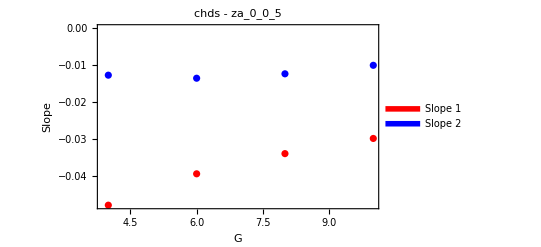

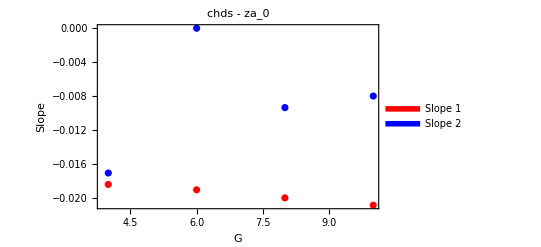

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
slopeList1 = List[];
slopeList2 = List[];
model ="chds"; 
Do[
name=model<>"/G_"<>ToString[G];
zName="za_0_0_5";
za=0.05;
n=1;
path1="polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2="polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3="polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
costRegretList={};
costs={};
averagedMetrics=GetAveragedMetrics[za,path1,path3,n,G];
accuracies=averagedMetrics[[1]];
regrets=averagedMetrics[[2]];
convergenceTimes=averagedMetrics[[3]];
Do[cost=(convergenceTimes[[k*20+1]][[2]])*(k+(1-k)*G);
AppendTo[costs,cost];,{k,0,1,0.05}];
Do[AppendTo[costRegretList,{costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]]}],{k,0,1,0.05}];

minimumK=-1;
minimumError=+Infinity;
Do[sublist2=Take[costRegretList,k*20];
sublist1=Drop[costRegretList,k*20];
fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];
error=fit1["EstimatedVariance"]+fit2["EstimatedVariance"];
If[error<minimumError,minimumK=k;minimumError=error],{k,0.1,0.95,0.05}];

sublist2=Take[costRegretList,minimumK*20];
sublist1=Drop[costRegretList,minimumK*20];

fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];
slope1=fit1["BestFitParameters"][[2,2]];
slope2=fit2["BestFitParameters"][[2,2]];
Print[slope1];
Print[slope2];
AppendTo[slopeList1, {G, slope1}];
AppendTo[slopeList2, {G, slope2}];
,{G, 4, 10, 2}]
plot = Show[ListPlot[{slopeList1,slopeList2}, PlotStyle->{Red, Blue},Frame->True,FrameLabel->{Style["G",Bold,Black,64],Style["Slope",Bold,Black,64]},FrameTicks->True,FrameTicksStyle->Directive[Black,Bold,32],ImageSize->Full,FrameStyle->Directive[Black,Bold], PlotLabel->Style[model<>" - "<>zName, Bold, Black, 64]]];
Legended[plot,Placed[LineLegend[{Directive[Red,Thickness[0.05]],Directive[Blue,Thickness[0.05]]},{Style["Slope 1", Bold, Black, 32],Style["Slope 2", Bold, Black, 32]}], {0.8,0.8}]]
```

### [exp] Plot inaccuracy and indecision

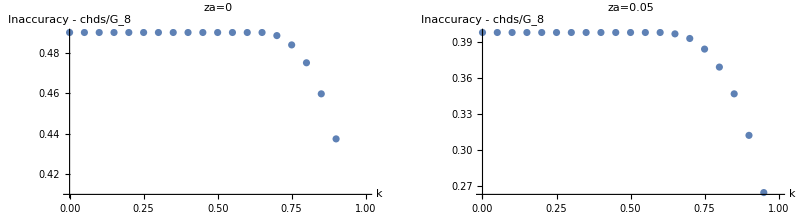

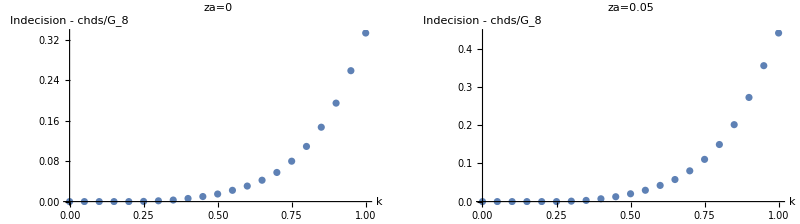

```mathematica
<<"/home/nema/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name = "chds/G_8";
zName = "za_0";
pathWA="polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
zName = "za_0_0_5";
pathDoS="polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
measuresWA=ExtractK[0, pathWA];
indecisionsWA = measuresWA[[7]];
inaccuraciesWA = measuresWA[[6]];
measuresDoS=ExtractK[0.05, pathDoS];
indecisionsDoS = measuresDoS[[7]];
inaccuraciesDoS = measuresDoS[[6]];
GraphicsRow[{Graphics[ListPlot[inaccuraciesWA, AxesLabel->{"k ","Inaccuracy - "<>name}, PlotLabel->"za="<>ToString[0]]],
			Graphics[ListPlot[inaccuraciesDoS, AxesLabel->{"k ","Inaccuracy - "<>name}, PlotLabel->"za="<>ToString[0.05]]]}]
GraphicsRow[{Graphics[ListPlot[indecisionsWA, AxesLabel->{"k ","Indecision - "<>name}, PlotLabel->"za="<>ToString[0]]],
			Graphics[ListPlot[indecisionsDoS, AxesLabel->{"k ","Indecision - "<>name}, PlotLabel->"za="<>ToString[0.05]]]}]
```

### Plot regret/cost plot with fitted lines

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chds/G_8";
G=8;
zName="za_0";
za=0.0;
zNameDoS ="za_0_0_5";
names={"chds/G_8", "chci/G_8"};
plotList=List[];
maxRegretAcross = 0.0;
minRegretAcross = +Infinity;
maxCostAcross = 0.0;
minCostAcross = +Infinity;
Do[
name=names[[nameIndex]];

path1 = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
n=1;

path1DoS = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zNameDoS<>"/";
path2DoS =  "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zNameDoS<>"/";
path3DoS = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zNameDoS<>"/";

costRegretList={};
averagedMetrics =GetAveragedMetrics[za, path1, path3, n, G];
accuracies = averagedMetrics[[1]];
regrets = averagedMetrics[[2]];
convergenceTimes = averagedMetrics[[3]];
costs={};
Print["convergenceTimes"];
Print[N[convergenceTimes]];
costRegretListDoS={};
averagedMetricsDoS =GetAveragedMetrics[0.05, path1DoS, path3DoS, n, G];
accuraciesDoS = averagedMetricsDoS[[1]];
regretsDoS = averagedMetricsDoS[[2]];
convergenceTimesDoS = averagedMetricsDoS[[3]];
costsDoS={};

Do[
	cost=(convergenceTimes[[k*20+1]][[2]](*+stds[[k*10+1]][[2]][[2]]*))*(k+(1-k)*G); 
   costDoS = (convergenceTimesDoS[[k*20+1]][[2]](*+stds[[k*10+1]][[2]][[2]]*))*(k+(1-k)*G); 
AppendTo[costs, cost];
AppendTo[costsDoS, costDoS];
, {k,0,1,0.05}];
costRegretPlotList = {};
costRegretPlotListDoS = {};
Do[
(*AppendTo[costRegretList, Labeled[{costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]]}, Text["k="<>ToString[k]]]]*)
AppendTo[costRegretList,{costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]]}];
AppendTo[costRegretPlotList, {costs[[Floor[20*k]+1]],regrets[[Floor[20*k]+1]][[2]], k }];
AppendTo[costRegretListDoS,{costsDoS[[Floor[20*k]+1]],regretsDoS[[Floor[20*k]+1]][[2]]}];
AppendTo[costRegretPlotListDoS, {costsDoS[[Floor[20*k]+1]],regretsDoS[[Floor[20*k]+1]][[2]], k }];
,{k,0,1,0.05}];

Print["costs wa: "];
Print[costs];
Print["costs with library:"];
Print[N[averagedMetrics[[4]]]];
Print["costs dos: "];
Print[costsDoS];
(*find points that lie on the same line*)
lastRegret = First[costRegretList][[2]];
sublist=Select[costRegretList,#[[2]]==lastRegret&];
ignorePlateau=False;
If[Length[sublist]==1,ignorePlateau=True, costRegretList=DeleteCases[costRegretList,Alternatives@@sublist]; Print["k wa = "<>ToString[N[(Length[sublist]-1)/20]]<>" length sublist wa: "<>ToString[Length[sublist]]];] ;
Print["costregretlist:"];
Print[costRegretList];
ignorePlateauDoS = False;
lastRegretDoS = First[costRegretListDoS][[2]];
sublistDoS=Select[costRegretListDoS,#[[2]]==lastRegretDoS&];
If[Length[sublistDoS]==1, ignorePlateauDoS = True, costRegretListDoS=DeleteCases[costRegretListDoS,Alternatives@@sublistDoS]; Print["k dos = "<>ToString[N[(Length[sublistDoS]-1)/20]]<>" length sublist dos: "<>ToString[Length[sublist]]]];



minimumK = -1;
minimumError = +Infinity;

minimumKDoS = -1;
minimumErrorDoS = +Infinity;
Do[
sublist2=Take[costRegretList,k*20+1];
sublist1=Drop[costRegretList,k*20];
fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];

sublist2DoS=Take[costRegretListDoS,k*20+1];
sublist1DoS=Drop[costRegretListDoS,k*20];
fit1DoS=NonlinearModelFit[sublist1DoS,a+b x,{a,b},x];
fit2DoS=NonlinearModelFit[sublist2DoS,a+b x,{a,b},x];

error = fit1["EstimatedVariance"]+fit2["EstimatedVariance"];
errorDoS = fit1DoS["EstimatedVariance"]+fit2DoS["EstimatedVariance"];
If[error<minimumError, minimumK=k;minimumError=error];
If[errorDoS<minimumErrorDoS, minimumKDoS=k;minimumErrorDoS=errorDoS];
,{k,0.1,0.95,0.05}];
sublist2=Take[costRegretList,minimumK*20+1];
sublist1=Drop[costRegretList,minimumK*20];

fit1=NonlinearModelFit[sublist1,a+b x,{a,b},x];
fit2=NonlinearModelFit[sublist2,a+b x,{a,b},x];
Print["minimum k wa:"];
Print[minimumK];
Print["fit1/2:"];
Print[fit1];
Print[fit2];
sublist2DoS=Take[costRegretListDoS,minimumKDoS*20+1];
sublist1DoS=Drop[costRegretListDoS,minimumKDoS*20];
Print["minimum k dos:"];
Print[minimumKDoS];
fit1DoS=NonlinearModelFit[sublist1DoS,a+b x,{a,b},x];
fit2DoS=NonlinearModelFit[sublist2DoS,a+b x,{a,b},x];
Print["fit1/2 dos:"];
Print[fit1DoS];
Print[fit2DoS];
maxRegret = Max[costRegretPlotList[[All, 2]], costRegretPlotListDoS[[All,2]]];
If[maxRegret>maxRegretAcross, maxRegretAcross=maxRegret];
minRegret =  Min[costRegretPlotList[[All, 2]], costRegretPlotListDoS[[All,2]]];
If[minRegret<minRegretAcross, minRegretAcross=minRegret];
maxCost =  Max[costRegretPlotList[[All, 1]], costRegretPlotListDoS[[All,1]]];
If[maxCost>maxCostAcross, maxCostAcross=maxCost];
minCost =Min[costRegretPlotList[[All, 1]], costRegretPlotListDoS[[All,1]]];
If[minCost<minCostAcross, minCostAcross=minCost];
colorList = Table[ColorData[{"DarkRainbow", {0,1}}][k],{k, 0, 1, 0.05}];
If[nameIndex==1,
styledtab=Style[{#,#2},PointSize[.04],ColorData[{"DarkRainbow",{0,1}}][#3] ]&@@@costRegretPlotList;
(*Scatter plot*)
scatterPlot=ListPlot[styledtab];
scatterPlotDoS=ListPlot[List /@ costRegretPlotListDoS[[All, {1,2}]], PlotStyle->colorList, PlotMarkers->{"■", 96}];
 legend = BarLegend["DarkRainbow",LegendLabel->Placed["swarm heterogeneity (k)", Above], LegendMarkerSize->{1700, 50}, LabelStyle->Directive[48, Black],  LegendLayout->"Row"];
scatterPlot = Legended[scatterPlot, Placed[legend,Above]];
(*Line plots for the best-fitting lines*)
linePlot1=Plot[fit1//Normal,{x,Min[sublist1[[All,1]]],Max[sublist1[[All,1]]]},PlotStyle->Directive[Red,Thickness[0.01]],PlotRange->All];
linePlot2=Plot[fit2//Normal,{x,Min[sublist2[[All,1]]],Max[sublist2[[All,1]]]},PlotStyle->Directive[Blue,Thickness[0.01]],PlotRange->All];
If[ignorePlateau, linePlot3 = Graphics[],linePlot3 = Plot[lastRegret, {x, Min[sublist[[All, 1]]], Max[sublist[[All, 1]]]}, PlotStyle->Directive[Green, Thickness[0.01]], PlotRange->All]];

linePlot1DoS=Plot[fit1DoS//Normal,{x,Min[sublist1DoS[[All,1]]],Max[sublist1DoS[[All,1]]]},PlotStyle->Directive[(*Light*)Red,Thickness[0.01]],PlotRange->All];
linePlot2DoS=Plot[fit2DoS//Normal,{x,Min[sublist2DoS[[All,1]]],Max[sublist2DoS[[All,1]]]},PlotStyle->Directive[(*Light*)Blue,Thickness[0.01]],PlotRange->All];
If[ignorePlateauDoS, linePlot3DoS=Graphics[],linePlot3DoS = Plot[lastRegretDoS, {x, Min[sublistDoS[[All, 1]]], Max[sublistDoS[[All, 1]]]}, PlotStyle->Directive[(*Light*)Green, Thickness[0.01]], PlotRange->All]],
(*else*)
scatterPlot=ListPlot[List /@ costRegretPlotList[[All, {1,2}]], PlotStyle->colorList, PlotMarkers->{"▲",  96}];
linePlot1=Plot[fit1//Normal,{x,Min[sublist1[[All,1]]],Max[sublist1[[All,1]]]},PlotStyle->Directive[Red,Thickness[0.01], Dashed],PlotRange->All];
linePlot2=Plot[fit2//Normal,{x,Min[sublist2[[All,1]]],Max[sublist2[[All,1]]]},PlotStyle->Directive[Blue,Thickness[0.01], Dashed],PlotRange->All];
If[ignorePlateau, linePlot3 = Graphics[],linePlot3 = Plot[lastRegret, {x, Min[sublist[[All, 1]]], Max[sublist[[All, 1]]]}, PlotStyle->Directive[Green, Thickness[0.01], Dashed], PlotRange->All]];
scatterPlotDoS=ListPlot[List /@ costRegretPlotListDoS[[All, {1,2}]], PlotStyle->colorList, PlotMarkers->{"◆", 96}];
linePlot1DoS=Plot[fit1DoS//Normal,{x,Min[sublist1DoS[[All,1]]],Max[sublist1DoS[[All,1]]]},PlotStyle->Directive[(*Light*)Red,Thickness[0.01], Dashed],PlotRange->All];
linePlot2DoS=Plot[fit2DoS//Normal,{x,Min[sublist2DoS[[All,1]]],Max[sublist2DoS[[All,1]]]},PlotStyle->Directive[(*Light*)Blue,Thickness[0.01], Dashed],PlotRange->All];
If[ignorePlateauDoS, linePlot3DoS=Graphics[],linePlot3DoS = Plot[lastRegretDoS, {x, Min[sublistDoS[[All, 1]]], Max[sublistDoS[[All, 1]]]}, PlotStyle->Directive[(*Light*)Green, Thickness[0.01], Dashed], PlotRange->All]]
];
pointsPlot = Show[{scatterPlot,scatterPlotDoS}];
AppendTo[plotList, pointsPlot];
AppendTo[plotList, linePlot1];
AppendTo[plotList, linePlot2];
AppendTo[plotList, linePlot3];
AppendTo[plotList, linePlot1DoS];
AppendTo[plotList, linePlot2DoS];
AppendTo[plotList, linePlot3DoS];
,{nameIndex, 1, Length[names]}]
```

convergenceTimes

{{0.,1.90811},{0.05,1.98385},{0.1,2.06613},{0.15,2.16494},{0.2,2.28105},{0.25,2.39192},{0.3,2.49018},{0.35,2.61049},{0.4,2.70213},{0.45,2.83534},{0.5,2.96956},{0.55,3.11483},{0.6,3.29829},{0.65,3.54035},{0.7,3.78907},{0.75,4.01337},{0.8,4.2555},{0.85,4.50631},{0.9,4.91356},{0.95,5.17852},{1.,6.5026}}

costs wa:

{15.2649,15.1765,15.0827,15.0463,15.0549,14.9495,14.6921,14.4882,14.0511,13.7514,13.363,12.9265,12.5335,12.2142,11.7461,11.0368,10.2132,9.23794,8.35306,6.991,6.5026}

costs with library:

{{0.,15.2649},{0.3825,15.1765},{0.73,15.0827},{1.0425,15.0463},{1.32,15.0549},{1.5625,14.9495},{1.77,14.6921},{1.9425,14.4882},{2.08,14.0511},{2.1825,13.7514},{2.25,13.363},{2.2825,12.9265},{2.28,12.5335},{2.2425,12.2142},{2.17,11.7461},{2.0625,11.0368},{1.92,10.2132},{1.7425,9.23794},{1.53,8.35306},{1.2825,6.991},{1.,6.5026}}

costs dos:

{16.0123,15.9412,15.8826,15.8426,15.8415,15.9434,15.7288,15.5605,15.1227,14.8295,14.3601,13.9331,13.4396,13.1201,12.5387,11.6976,10.8374,9.70445,7.95938,5.94821,4.2866}

k wa = 0.2 length sublist wa: 5

costregretlist:

{{14.9495,0.160515},{14.6921,0.161669},{14.4882,0.163206},{14.0511,0.166282},{13.7514,0.170127},{13.363,0.175125},{12.9265,0.18243},{12.5335,0.190888},{12.2142,0.202422},{11.7461,0.21634},{11.0368,0.234502},{10.2132,0.256448},{9.23794,0.28313},{8.35306,0.316355},{6.991,0.362561},{6.5026,0.418385}}

k dos = 0.25 length sublist dos: 5

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 1. Some property values cannot be computed.

General::stop: Further output of FittedModel::dof will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

General::stop: Further output of FittedModel::varzero will be suppressed during this calculation.

Take::take: Cannot take positions 1 through 16 in {{15.7288,0.117878},{15.5605,0.1198},{15.1227,0.124029},{14.8295,0.129412},{14.3601,0.137101},{13.9331,0.146328},{13.4396,0.159016},{13.1201,0.173403},{12.5387,0.192987},{11.6976,0.216501},«5»}.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Take::take: Cannot take positions 1 through 17 in {{14.9495,0.160515},{14.6921,0.161669},{14.4882,0.163206},{14.0511,0.166282},{13.7514,0.170127},{13.363,0.175125},{12.9265,0.18243},{12.5335,0.190888},{12.2142,0.202422},{11.7461,0.21634},«6»}.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Take::take: Cannot take positions 1 through 17 in {{15.7288,0.117878},{15.5605,0.1198},{15.1227,0.124029},{14.8295,0.129412},{14.3601,0.137101},{13.9331,0.146328},{13.4396,0.159016},{13.1201,0.173403},{12.5387,0.192987},{11.6976,0.216501},«5»}.

General::stop: Further output of Take::take will be suppressed during this calculation.

Drop::drop: Cannot drop positions 1 through 16 in {{15.7288,0.117878},{15.5605,0.1198},{15.1227,0.124029},{14.8295,0.129412},{14.3601,0.137101},{13.9331,0.146328},{13.4396,0.159016},{13.1201,0.173403},{12.5387,0.192987},{11.6976,0.216501},«5»}.

Drop::drop: Cannot drop positions 1 through 17 in {{14.9495,0.160515},{14.6921,0.161669},{14.4882,0.163206},{14.0511,0.166282},{13.7514,0.170127},{13.363,0.175125},{12.9265,0.18243},{12.5335,0.190888},{12.2142,0.202422},{11.7461,0.21634},«6»}.

Drop::drop: Cannot drop positions 1 through 17 in {{15.7288,0.117878},{15.5605,0.1198},{15.1227,0.124029},{14.8295,0.129412},{14.3601,0.137101},{13.9331,0.146328},{13.4396,0.159016},{13.1201,0.173403},{12.5387,0.192987},{11.6976,0.216501},«5»}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

minimum k wa:

0.25

fit1/2:

FittedModel[0.600117-0.0326856 x]

FittedModel[0.296516-0.00917017 x]

minimum k dos:

0.25

fit1/2 dos:

FittedModel[0.614989-0.0338609 x]

FittedModel[0.362588-0.0156474 x]

convergenceTimes

{{0.,2.77124},{0.05,2.8466},{0.1,2.91811},{0.15,2.99577},{0.2,3.09035},{0.25,3.18454},{0.3,3.29296},{0.35,3.40946},{0.4,3.5271},{0.45,3.65629},{0.5,3.79623},{0.55,3.93695},{0.6,4.10154},{0.65,4.24798},{0.7,4.42763},{0.75,4.61494},{0.8,4.79514},{0.85,5.05599},{0.9,5.29145},{0.95,5.64904},{1.,5.97939}}

costs wa:

{22.1699,21.7765,21.3022,20.8206,20.3963,19.9034,19.4285,18.9225,18.3409,17.733,17.083,16.3383,15.5858,14.6555,13.7257,12.6911,11.5083,10.3648,8.99547,7.6262,5.97939}

costs with library:

{{0.,22.1699},{0.3825,21.7765},{0.73,21.3022},{1.0425,20.8206},{1.32,20.3963},{1.5625,19.9034},{1.77,19.4285},{1.9425,18.9225},{2.08,18.3409},{2.1825,17.733},{2.25,17.083},{2.2825,16.3383},{2.28,15.5858},{2.2425,14.6555},{2.17,13.7257},{2.0625,12.6911},{1.92,11.5083},{1.7425,10.3648},{1.53,8.99547},{1.2825,7.6262},{1.,5.97939}}

costs dos:

{23.7601,23.3794,22.9244,22.5655,22.0939,21.6647,21.1434,20.6125,20.0263,19.4168,18.8339,18.0941,17.3767,16.4237,15.5387,14.4345,13.3591,12.106,10.9614,9.34033,7.55161}

costregretlist:

{{22.1699,0.236178},{21.7765,0.237916},{21.3022,0.238893},{20.8206,0.240384},{20.3963,0.24133},{19.9034,0.242753},{19.4285,0.24529},{18.9225,0.24559},{18.3409,0.247782},{17.733,0.248989},{17.083,0.250373},{16.3383,0.253041},{15.5858,0.254256},{14.6555,0.25867},{13.7257,0.263883},{12.6911,0.270727},{11.5083,0.280146},{10.3648,0.288328},{8.99547,0.298462},{7.6262,0.308428},{5.97939,0.318008}}

minimum k wa:

0.65

fit1/2:

FittedModel[0.361194-0.00704763 x]

FittedModel[0.299367-0.00283482 x]

minimum k dos:

0.55

fit1/2 dos:

FittedModel[0.375016-0.0093224 x]

FittedModel[0.26183-0.00296464 x]

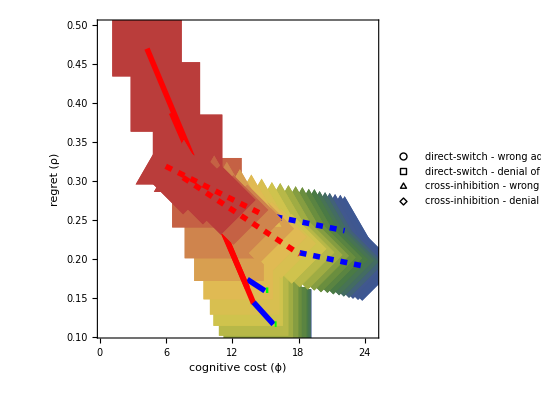

```mathematica
epsX = 1;
epsY = 0.01;
(*Show the plots together*)
plot = Show[plotList, AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["cognitive cost (ϕ)", Bold, Black, 48],Style["regret (ρ)", Bold, Black, 48]},FrameTicks->True, FrameTicksStyle->Directive[Black, 48],(*PlotLabel->Style[name<>" - "<>zName<>" breaking point="<>ToString[minimumK], Black, Bold, 32],*)
ImageSize->Full, FrameStyle->Directive[Black], PlotRange->{{minCostAcross-4*epsX, maxCostAcross+epsX}, {minRegretAcross-epsY, maxRegretAcross+2*epsY}}, AspectRatio->1];
legend = PointLegend[{Black, Black, Black, Black},{Style["direct-switch - wrong addressing", 32, Black, Bold], Style["direct-switch - denial of service", 32, Black, Bold], Style["cross-inhibition - wrong addressing", 32, Black, Bold], Style["cross-inhibition - denial of service", 32, Black, Bold]},LegendMarkers->{{"○", 45}, {"□", 64}, {"△", 64}, {"◇", 64}}, LegendLayout->(Column[Grid[{##},Alignment->{Center,Center}]&/@#,Spacings->{20,0}]&)];
plt  =Legended[plot,LineLegend[{Directive[Red,Thickness[0.05]],Directive[Blue,Thickness[0.05]], If[Not[ignorePlateau],Directive[Green, Thickness[0.05]], None],Directive[LightRed,Thickness[0.05]],Directive[LightBlue,Thickness[0.05]], If[Not[ignorePlateauDoS],Directive[LightGreen, Thickness[0.05]], None]},{Style[ToString[fit1//Normal], 32],Style[ToString[fit2//Normal], 32], If[Not[ignorePlateau],Style[ToString[lastRegret], 32], None],Style[ToString[fit1DoS//Normal], 32],Style[ToString[fit2DoS//Normal], 32], If[Not[ignorePlateauDoS],Style[ToString[lastRegretDoS], 32], None]}]];
plt2 = Legended[plot, Placed[legend, {0.65,0.87}]]
(*Export["/home/nema/extended_paper_figures/figures_after_22_11_23/3A.pdf", plt2];*)
Rasterize[plt2];
(*Graphics[Circle[{0,0},10]], Graphics[Rectangle[{200,200}, Offset[{-20,-20}]]]*)
```

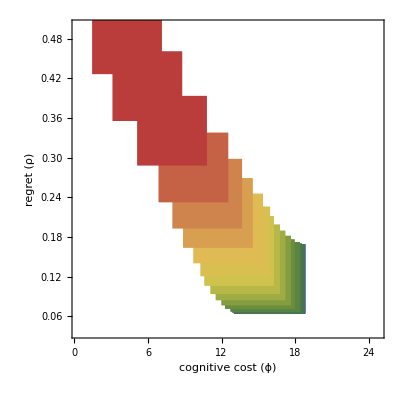

```mathematica
Show[plotList[[1]], AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["cognitive cost (ϕ)", Bold, Black, 48],Style["regret (ρ)", Bold, Black, 48]},FrameTicks->True, FrameTicksStyle->Directive[Black, 48],(*PlotLabel->Style[name<>" - "<>zName<>" breaking point="<>ToString[minimumK], Black, Bold, 32],*)
ImageSize->Full, FrameStyle->Directive[Black], PlotRange->{{minCostAcross-4*epsX, maxCostAcross+epsX}, {minRegretAcross-4*epsY, maxRegretAcross+epsY}}, AspectRatio->1]
```

```mathematica
<<"/home/nema/personal/polimi/Magistrale/secondo_anno/thesis/notebooks/plotK.wl"
name="chds/G_8";
G=8;
zName="za_0";
za=0.0;
zNameDoS ="za_0_0_5";
names={"chds/G_8", "chci/G_8"};
name=names[[1]];
zName="za_0";
plotList=List[];
maxRegretAcross = 0.0;
minRegretAcross = +Infinity;
maxCostAcross = 0.0;
minCostAcross = +Infinity;


path1 = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_a/"<>zName<>"/";
path2 =  "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/equal/"<>zName<>"/";
path3 = "personal/polimi/Magistrale/secondo_anno/thesis/notebooks/"<>name<>"/more_b/"<>zName<>"/";
n=1;

costRegretList={};
averagedMetrics =GetAveragedMetrics[za, path1, path3, n, G];
```

```mathematica
averagedMetrics[[2]]
```

{{0.,0.160131},{0.05,0.160131},{0.1,0.160131},{0.15,0.160131},{0.2,0.160131},{0.25,0.160515},{0.3,0.161669},{0.35,0.163206},{0.4,0.166282},{0.45,0.170127},{0.5,0.175125},{0.55,0.18243},{0.6,0.190888},{0.65,0.202422},{0.7,0.21634},{0.75,0.234502},{0.8,0.256448},{0.85,0.28313},{0.9,0.316355},{0.95,0.362561},{1.,0.418385}}